# GH, SHEL and OIF Shifts: Single Interface M. T. Lusk Last Edited: August 30, 2016

-Graphics-

## Plotting Tools

```mathematica
Clear[font,coloredfont];
font[name_,size_]:=Style[name,FontFamily->"Tahoma",FontSize->size,Bold]

coloredfont[name_,size_,color_]:=Style[name,FontFamily->"Helvetica",FontSize->size,Bold, color]
```

## Theory

### Basic Theory of Modal Representation of the E-Field

References:

[1] An angular spectrum representation approach to the Goos-Hanchen shift, M. McGuirk and C. K. Carniglia, J.Opt. Soc. Am. Vol 67(1) p 103 1977 [Spectral_Decomposition_McGuirk_JOSA_1977.pdf]

[2] Optical Coherence and Quantum Optics, Mandel and Wolf [Quantum_Optics_Mandel_Wolf.pdf]

McGuirk gives the key result and some hints about the proof, while Mandel gives a step-by-step detailed proof. See Mandel p111 Eq 3.2-12. This is the derivation repeated below.

Consider a beam characterized by

E⃗[r⃗,t]=E[r⃗] f ⅇ^(ⅈ(k_0·r- ω t))

Here f is the fixed polarization of the beam. This is a monchromatic beam since there is only 1 temporal frequency, ω. Since k_0=k_0 κ_0, we immediately have that k_0=ω/c. The beam can be decomposed into plane waves via a Fourier transform, but the magnitude of each wave vector must be k_0 because both the speed and temporal frequency are fixed. Thus, the E-field can be described in terms of a spectrum of mono-length wave vectors:

k=k_0 κ.

Suppose our incident beam, traveling with central wave vector, k_0, makes an angle of θ with a planar interface with unit normal, n̂.

It will be convenient to define the beam frame, which is fixed once θ is prescribed. Let u_3 be the unit vector along the beam axis. Then

u_2= n×u_3

u_1= u_2×u_3

Note that (û)_2 is normal to the plane of incidence (which is the plane containing (û)_3 and n̂), so E-fields in this direction are TE (s-polarized). Therefore E-fields in the (û)_1 direction are TM (p-polarized). The polarization of the beam is then

f= f_1 u_1+f_2 u_2.

Coordinates along each beam axis will be referred to as x, y, and z respectively.

Suppose that |k|=k_0. This implies that

k= k_0(κ_x u_1 +κ_y u_2  + √(1-κ_x^2-κ_y^2)u_3).

Consider the z = z_0 plane, where z_0 is completely arbitrary, and define the angular spectrum, Ẽ[κ_x,κ_y;z_0], as:

Ẽ[κ_x,κ_y;z_0]=∫∫ⅆx'ⅆy' E[x',y',z_0]ⅇ^(-ⅈ κ_x x')ⅇ^(-ⅈ κ_y y').

Then, as shown below,

E[x,y,z]=(1/(2π))^2∫∫ⅆ κ_xⅆ κ_yẼ[κ_x,κ_y;z]ⅇ^(ⅈ κ_x x)ⅇ^(ⅈ κ_y y)

Note that we can and have dropped the subscript on z.

Proof:

E[x,y,z_0]= (1/(2π))^2∫∫ⅆ k_xⅆ k_y∫ⅆx'ⅆy' E[x',y',z_0]ⅇ^(-ⅈ κ_x x')ⅇ^(ⅈ κ_x x)ⅇ^(-ⅈ κ_y y')ⅇ^(ⅈ κ_y y)

E[x,y,z_0]= (1/(2π))^2∫∫ⅆ κ_xⅆ κ_y∫ⅆx'ⅆy' E[x',y',z_0]ⅇ^(ⅈ κ_x(x-x'))ⅇ^(ⅈ κ_y(y-y'))

E[x,y,z_0]= ∫ⅆx'ⅆy' E[x',y',z_0]δ[x-x']δ[y-y']

E[x,y,z_0]= E[x,y,z_0]

This result can be used to construct a general spectral representation of the E-field. First note that

(∇^2 +κ^2)E[r]=0

Substitute our Fourier expression into this Helmholtz equation and reverse the order of integration and differentiation:

(1/(2π))^2∫∫ⅆ κ_xⅆ κ_y(∇^2 +κ^2)(Ẽ[κ_x,κ_y;z]ⅇ^(ⅈ κ_x x)ⅇ^(ⅈ κ_y y))=0

(1/(2π))^2∫∫ⅆ κ_xⅆ κ_y((-κ_x^2-κ_y^2+1+∂_zz)Ẽ[κ_x,κ_y;z])ⅇ^(ⅈ κ_x x)ⅇ^(ⅈ κ_y y))=0

Since this holds for all values of x and y, the integrand must be zero implying that

(∂_zz + κ_z^2)Ẽ[κ_x,κ_y;z]=0

The general solution to this equation is

Ẽ[κ_x,κ_y;z]= A[κ_x,κ_y]ⅇ^(ⅈ κ_z z)+B[κ_x,κ_y]ⅇ^(-ⅈ κ_z z)

Substitution of this result into the expression for E gives

E[x,y,z]=(1/(2π))^2∫∫ⅆ κ_xⅆ κ_yA[κ_x,κ_y]ⅇ^(ⅈ (κ_x x+κ_y y +κ_z z))+(1/(2π))^2∫∫ⅆ κ_xⅆ κ_yB[κ_x,κ_y]ⅇ^(ⅈ (κ_x x+κ_y y-κ_z z))

This is not a Fourier decomposition of the beam. Rather, it is a modal representation of the beam that only superficially resembles a Fourier transform.

The final expression is

E(r)≡E(r)f= (∑_(λ=1,2) u_λ f_λ)∫∫∫ⅆ k_xⅆ k_yⅆ k_z Ẽ(k)ⅇ^(ⅈ(k·r))

### Derivation of Reflected E-field

The unit normal of the plane is

n= -Sin[θ]u_1+Cos[θ]u_3

κ ... the normalized wave vector for each plane wave element of the incident beam. The coordinate basis chosen {u_1, u_2, u_3}, is that of the beam with the plane of incidence that which contains interface normal, n, and u_3.

u_(1') ... TM/1/p polarization of an individual plane wave element
u_(2') ... TE/2/s polarization of an individual plane wave element
u_(3') ... direction of propagation of an individual plane wave element

Construct a set of linearized relations in which the primed basis vectors are expressed in terms of the beam basis vectors. (Eq 19 of Bliokh PRE 2007).

```mathematica
Clear[κvec,κx,κy,κz,e1,e2];

κvec = {κx ,κy,√(1-κx^2-κy^2)};

nvec = {-Sin[θ],0,Cos[θ]};

u2prime= Cross[nvec,κvec]/(√(Cross[nvec,κvec].Cross[nvec,κvec]));

u1prime  =Simplify[ Cross[u2prime,κvec]/(√(Cross[u2prime,κvec].Cross[u2prime,κvec]))];

u1prime=FullSimplify[Expand[Normal[Series[u1prime,{κx,0,1},{κy,0,1}]]]/. {κx^2->0,κy^2->0,κx κy->0},{θ>0,θ<π/2}]

u2prime=FullSimplify[Expand[Normal[Series[u2prime,{κx,0,1},{κy,0,1}]]]/. {κx^2->0,κy^2->0,κx κy->0},{θ>0,θ<π/2}]

u3prime= Cross[u1prime,u2prime]/.{κx^2->0,κy^2->0,κx κy->0}
```

{1,κy Cot[θ],-κx}

{-κy Cot[θ],1,-κy}

{κx,κy,1}

The physical polarization of each plane wave element is taken to be the same as that of the beam, so the polarization does not change from plane wave to plane wave. Instead, the electric field of each plane wave is expressed in terms of the Fourier transform of the scalar E-field of the beam. Call this Ẽ so that

E=E e

Ẽ=ℱ[E]

Ẽ=Ẽ e = Ẽ (f_1 u_1+f_2 u_2)

where f is the polarization vector of the beam.

But we can also write

Ẽ=(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2') + (Ẽ)_z' u_(3')

Since

u_(1')=u_1+κ_y Cot[θ]u_2-κ_x u_3

u_(2')=-κ_y Cot[θ]u_1+u_2-κ_y u_3

u_(3')=κ_x u_1+κ_y u_2+u_3

Now invert these equations to obtain the unprimed basis vectors in terms of their primed counterparts.

```mathematica
sol=Simplify[Solve[{
u1p == {u1,u2,u3}.u1prime ,
u2p =={u1,u2,u3}.u2prime,
u3p =={u1,u2,u3}.u3prime
},{u1,u2,u3}]];

Expand[sol] /. {κx^2->0,κy^2->0,κx κy->0}
```

{{u1→u1p+u3p κx-u2p κy Cot[θ],u2→u2p+u3p κy+u1p κy Cot[θ],u3→u3p-u1p κx-u2p κy}}

We have two ways of writing the E-field:

Ẽ= Ẽ (f_1 u_1+f_2 u_2)=(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2')

Using the relations derived above, equate the components.

(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2') =Ẽ (f_1(u_(1')-κ_y Cot[θ]u_(2')+κ_x u_(3'))+ f_2(κ_y Cot[θ]u_(1')+u_(2')+κ_y u_(3')))

(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2') =Ẽ (f_1+f_2 κ_y Cot[θ])u_(1')+Ẽ (f_2-f_1 κ_y Cot[θ])u_(2') + Ẽ (f_1 κ_x+f_2 κ_y)u_(3'))

This implies that

(Ẽ)_x' =Ẽ (f_1+f_2 κ_y Cot[θ])

(Ẽ)_y' =Ẽ (f_2-f_1 κ_y Cot[θ])

It also leaves a u_(3') component that sums to zero when all plane waves are taken into account.

Not surprisingly, we can recover our original formulation of the incident field:

```mathematica
Etilde = Etildemag Expand[( f1 + κy Cot[θ] f2) u1prime+(f2 - κy Cot[θ]f1) u2prime] /. {κy^2->0,κx κy ->0}
```

{Etildemag f1,Etildemag f2,Etildemag (-f1 κx-f2 κy)}

That is not the point though. We did this in order to be able to apply polarization-dependent reflection coefficients to each plane-wave vector.

The (Ẽ)_x' is multiplied by R_1, while the (Ẽ)_y' component is multiplied by R_2. We also need to constructed the primed unit vectors, here expressed in terms of the original incident angle although we could have put in θR directly. Later we will re-write the final result in terms of θR.

```mathematica
u1prime

u2prime
```

{1,κy Cot[θ],-κx}

{-κy Cot[θ],1,-κy}

```mathematica
u1prime$R = u1prime/. {θ->π-θ}
u2prime$R = u2prime/. {θ->π-θ}
```

{1,-κy Cot[θ],-κx}

{κy Cot[θ],1,-κy}

```mathematica
Clear[u1prime$R,u2prime$R];

u1prime$R = u1prime
u2prime$R = u2prime
```

{1,κy Cot[θ],-κx}

{-κy Cot[θ],1,-κy}

```mathematica
Etilde = Etildemag Expand[( f1 + κy Cot[θ] f2) u1prime+(f2 - κy Cot[θ]f1) u2prime] /. {κy^2->0,κx κy ->0}
```

```mathematica
Clear[R1,R2];

Etilde$R = Simplify[Etildemag Expand[( f1 + κy Cot[π-θ] f2) u1prime$R (R1)+(f2 - κy Cot[π-θ]f1) u2prime$R R2] /. {κy^2->0,κx κy ->0}]
```

{Etildemag (f1 R1-f2 (R1+R2) κy Cot[θ]),Etildemag (f2 R2+f1 (R1+R2) κy Cot[θ]),-Etildemag (f1 R1 κx+f2 R2 κy)}

The final expression is therefore:

(Ẽ)_R= Ẽ((f_1 R_1-f_2 κ_y Cot[θ](R_1+R_2))u_1+(f_2 R_2 + f_1 κ_y Cot[θ](R_1+R_2 ))u_2-(f_1 R_1 κ_x + f_2 R_2  κ_y)u_3

Since the basis vectors are constant for a given beam, the reflected beam is easily recovered by just taking the inverse Fourier transform of each of its components above.

### Aside: Reflected Polarization Vector

As an aside, we also recover Bliokh’s polarization vector for plane wave elements of the reflected beam.

```mathematica
etildeR = Simplify[Expand[1/Etildemag Etilde$R ]/. {κy^2->0,κx κy ->0}]
```

{f1 R1-f2 (R1+R2) κy Cot[θR],f2 R2+f1 (R1+R2) κy Cot[θR],-f1 R1 κx-f2 R2 κy}

Replace f1 with 1, f2 with mc, and remember that Bliokh’s (m̃)^R ≡ m_c ρR. Then it clear that the line above is the same as Bliokh’s Eq 40 (below) once it is normalized.

-Graphics-

### Aside: Construction of Formulae for the Goos-Hanchen Shifts

The work below does not derive Artmann’s formula for the GH shift. Rather, Artmann’s formula is used to get an explicit expression for the GH shift. However, in the application section in which a Gaussian beam is considered analytically, I derive Artmann’s formula explicitly by analytically calculating the centroid of the reflected beam. (That was fun and cool to do!)

Start by defining the two reflection coefficients. These will be complex valued for angles of incidence greater than the critical angle. The existence of a critical angle implies that n_2 < n_1--i.e. that the wave impinges on a material with a lower dielectric constant.

```mathematica
Clear[R1,R2,β,n];

R2=(Cos[β]-√(n^2-Sin[β]^2))/(Cos[β]+√(n^2-Sin[β]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(-n^2 Cos[β]+√(n^2-Sin[β]^2))/(n^2 Cos[β]+√(n^2-Sin[β]^2));(* Fresnel Reflection Coefficient: p/TM *)
```

The GH shift can be estimated from the phase of these reflection coefficients. These phases, in turn, can be obtained in an analytically simple form or just by brute force. The approaches are shown to be equivalent below.

The brute force approach is:

```mathematica
Clear[Φ1,Φ2];

Φ1[β_,n_]=FullSimplify[ArcTan[Re[R1 /. {κx->0,κy->0}],Im[R1 /. {κx->0,κy->0}]]];

Φ2[β_,n_]=FullSimplify[ArcTan[Re[R2 /. {κx->0,κy->0}],Im[R2 /. {κx->0,κy->0}]]];
```

The derivative of these expressions with respect to β gives the GH shift:

GH_λ := (∂_β Φ_λ)/k_0

This is written in the coordinate system of the reflected beam, and the shift will come out to be negative. This is still “up and to the right” in our fixed frame though. If we use the expressions for Φ directly, the resulting formulae are ugly and do not offer any insights. We can analytically derive equivalent phase representations, with only a little effort, that work much better. First separate the reflection coefficients into real and imaginary parts.

```mathematica
((-n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2))/(n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2)))((n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2))/(n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2)))
```

(-n^2 Cos[β]+ⅈ √(-n^2+Sin[β]^2))/(n^2 Cos[β]+ⅈ √(-n^2+Sin[β]^2))

```mathematica
((-n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2))(n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2))
```

((n^2 Cos[β]-ⅈ √(-n^2+Sin[β]^2)) (-n^2 Cos[β]+ⅈ √(-n^2+Sin[β]^2)))/(-n^2+n^4 Cos[θ]^2+Sin[θ]^2)

```mathematica
R1$analytic=(-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2)+ⅈ 2 n^2 Cos[β] √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2);
```

```mathematica
R2$analytic=((Cos[θ])^2-2ⅈ Cos[θ] √(1-n^2-Cos[θ]^2)-(1-n^2-Cos[θ]^2))/((Cos[θ])^2+1-n^2-Cos[θ]^2);
```

Then the phases are

```mathematica
Clear[Φ1$analytic];
Φ1$analytic[θ_,n_]=FullSimplify[ArcTan[-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2),2 n^2 Cos[θ] √(Sin[θ]^2-n^2)] ,{θ>0,n>0,(Sin[θ]^2-n^2)>0}]
```

ArcTan[-n^2-n^4 Cos[θ]^2+Sin[θ]^2,2 n^2 Cos[θ] √(-n^2+Sin[θ]^2)]

```mathematica
Clear[Φ2$analytic];
Φ2$analytic[θ_,n_]=FullSimplify[ArcTan[(Cos[θ])^2-(1-n^2-Cos[θ]^2),-2Cos[θ] √(1-n^2-Cos[θ]^2)] ,{θ>0,n>0,1-n^2-Cos[θ]^2>0}]
```

ArcTan[n^2+Cos[2 θ],-2 Cos[θ] √(1-n^2-Cos[θ]^2)]

Below is a comparison of the two expressions for Φ_1. They are clearly equivalent.

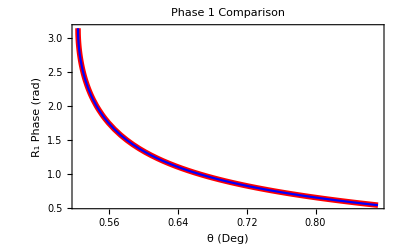

```mathematica
Plot[{Φ1[θ,1/2],Φ1$analytic[θ,1/2]},{θ,30 Degree, 50 Degree},PlotStyle->{{Thickness[.01],Red},Blue},Frame->True,FrameLabel->{font["θ (Deg)",10],font["R_1 Phase (rad)",10]},PlotLabel->font["Phase 1 Comparison",14]]
```

Below is a comparison of the two expressions for Φ_2. They are clearly equivalent.

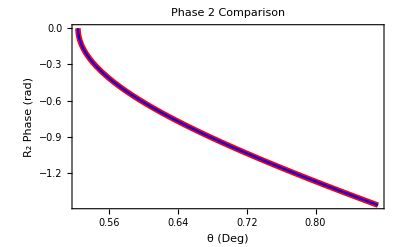

```mathematica
Plot[{Φ2[θ,1/2],Φ2$analytic[θ,1/2]},{θ,30 Degree, 50 Degree},PlotStyle->{{Thickness[.01],Red},Blue},Frame->True,FrameLabel->{font["θ (Deg)",10],font["R_2 Phase (rad)",10]},PlotLabel->font["Phase 2 Comparison",14]]
```

These formula can be used to calculate the GH shifts for each polarization using Artmann’s formulae:

```mathematica
Clear[GHshift$1,GHshift$2];
GHshift$1[θ_,n_]=1/k0 FullSimplify[D[Φ1$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]

GHshift$2[θ_,n_]=1/k0 FullSimplify[D[Φ2$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]
```

(4 n^2 Sin[θ])/(k0 (-1+n^2+(1+n^2) Cos[2 θ]) √(-n^2+Sin[θ]^2))

-(2 √2 Sin[θ])/(k0 √(1-2 n^2-Cos[2 θ]))

These are very small shifts in general. For instance, for 600 nm light and n = 0.5, the critical angle is 30°. At 35°, the GH shift for polarization 1 is only 600 nm. This is shown below.

```mathematica
Print["GH_1 for 600 nm light: ",GHshift$1[35. Degree,1/2]/. k0->2π/(600.0*10^-9)," meters"]
```

GH_1 for 600 nm light: -6.0434×10^-7 meters

Here is a plot of the GH shifts for both polarizations.

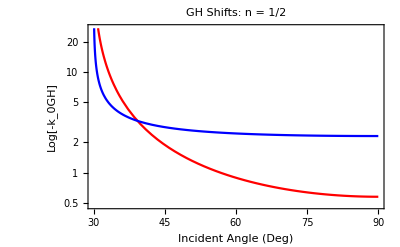

```mathematica
LogPlot[{-k0 GHshift$1[θ Degree,1/2],-k0 GHshift$2[θ Degree,1/2]},{θ,30 , 90 },PlotStyle->{Red,Blue},Frame->True,PlotLabel->font["GH Shifts: n = 1/2",14],FrameLabel->{font["Incident Angle (Deg)",12],font["Log[-k_0GH]",12]},GridLines->Automatic]
```

Here is the same plot but now in units for 600 nm incident light.

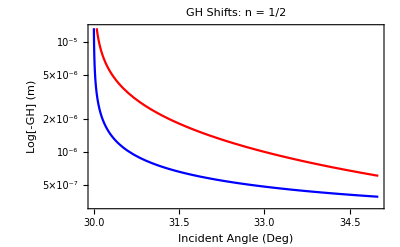

```mathematica
k0set = 2π/(600.*10^-9);

LogPlot[{-GHshift$1[θ Degree,1/2]/. k0->k0set,-GHshift$2[θ Degree,1/2]/. k0->k0set},{θ,30 , 35 },PlotStyle->{Red,Blue},Frame->True,PlotLabel->font["GH Shifts: n = 1/2",14],FrameLabel->{font["Incident Angle (Deg)",12],font["Log[-GH] (m)",12]},GridLines->Automatic]
```

## Applications

### Construction of E-field in Paraxial Approximation: Must Run Each Time

r … radial distance from the center axis of the beam

z … axial distance from the beam’s focus (or “waist”)

z_R… Rayleigh Range, π w0^2/λ

k = 2 π/λ  … wave number (in radians per meter) for a wavelength λ

E0 ≡ E(0,0) … electric field amplitude (and phase) at the origin at time 0

w(z) … radius at which the field amplitudes fall to 1/e of their axial values, at the plane z along the beam

w0 = w(0) … waist size

R(z) … radius of curvature of the beam’s wavefronts at z

ψ(z) … the Gouy phase at z, an extra phase term beyond that attributable to the phase velocity of light

p ... radial index ≥ 0

ℓ … azimuthal mode index ≥ 0

Nmax ... combined mode number, Nmax = |ℓ| + 2 p

There is also an understood time dependence e^(ⅈ ω t) multiplying such phasor quantities; the actual field at a point in time and space is given by the real part of that complex quantity.

```mathematica
Clear[Escalar,r,φfunc,z,w,w0,zR,λ,k,R,ψ,Nmax,Evec,k0];

ω = c1 k0;

r[x_,y_]=Sqrt[x^2+y^2];
φfunc[x_,y_]=ArcTan[x,y];

λ = 2 π/k0;

zR = π w0^2/λ;

w[z_]=w0 √(1+(z/zR)^2);

R[z_]=Simplify[z(1 + (zR/z)^2)];

Nmax = 2 p+Abs[ℓ];

ψ[z_]=(Nmax+1)ArcTan[zR,z];


Escalar[x_,y_,z_]=Simplify[1/w[z] Exp[(-(x^2+y^2))/w[z]^2]Exp[-ⅈ (k0 (x^2+y^2)/(2 R[z])+ k0 z+ψ[z])]((r[x,y] √2)/w[z])^Abs[ℓ] LaguerreL[p,Abs[ℓ],(2(x^2+y^2))/w[z]^2]Exp[-ⅈ ℓ φfunc[x,y]],{Element[x,Reals],Element[y,Reals],Element[z,Reals]}];
```

```mathematica
Escalar2D[x_,y_]=FullSimplify[Escalar[x,y,0],{k0>0,w0>0}] /. w0 ->wk/k0
```

(2^(Abs[ℓ]/2) ⅇ^(-(k0^2 (x^2+y^2))/wk^2-ⅈ ℓ ArcTan[x,y]) k0 (k0/(wk √(1/(x^2+y^2))))^Abs[ℓ] LaguerreL[p,Abs[ℓ],(2 k0^2 (x^2+y^2))/wk^2])/wk

### Key Fields: Must Run Each Time

```mathematica
Clear[κvec,κx,κy,κz];

κvec = {κx ,κy,√(1-κx^2-κy^2)};

κvec0 = {0,0,1};


nvec = {-Sin[θ],0,Cos[θ]};
```

### Fresnel Coefficients: Must Run Each Time

```mathematica
Clear[R1,R2,β,n];

β =ArcCos[κvec.nvec];

R2=(Cos[β]-√(n^2-Sin[β]^2))/(Cos[β]+√(n^2-Sin[β]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(n^2 Cos[β]-√(n^2-Sin[β]^2))/(n^2 Cos[β]+√(n^2-Sin[β]^2));(* Fresnel Reflection Coefficient: p/TM *)

T2=Simplify[(2Cos[β])/(Cos[β]+√(n^2-Sin[β]^2))];(* Fresnel Transmission Coefficient: s/TE *)

T1=Simplify[(2n Cos[β])/(n^2 Cos[β]+√(n^2-Sin[β]^2))];(* Fresnel Transmission Coefficient: p/TM *)
```

```mathematica
R1 /. {κx->0,κy->0}
```

(n^2 Cos[θ]-√(-1+n^2+Cos[θ]^2))/(n^2 Cos[θ]+√(-1+n^2+Cos[θ]^2))

```mathematica
θbrewster = ArcTan[n]
```

ArcTan[n]

```mathematica
Simplify[R1/. θ->θbrewster/. {κx->0,κy->0},{n>0}]

Simplify[R2/. θ->θbrewster/. {κx->0,κy->0},{n>0}]
```

0

(1-n^2)/(1+n^2)

```mathematica
θbrewster/Degree/. n->1.5168
```

56.6038

### Centroid Shifts versus Angle of Incidence: n = 1.5168, OAM = 0 (Air/Glass) FIG 2

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.5
```

33.6901

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

```mathematica
θcrit = ArcSin[n]/Degree /. n->1/1.5
```

41.8103

#### Analysis

```mathematica
Clear[plots,k0];

fontset = 6;

IFshift$tab$R1 = {};
IFshift$tab$R2 = {};
IFshift$tab$R3 = {};
IFshift$tab$R4 = {};
IFshift$tab$T1 = {};
IFshift$tab$T2 = {};
IFshift$tab$T3 = {};
IFshift$tab$T4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1.5168,θ->θloop Degree,k0->1,p->0,ℓ->0};

Print["Angle of Incidence: ",θloop,"°"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)

Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eR = {(f[[1]]R1-f[[2]]κy Cot[θ](R1+R2)),f[[2]]R2 + f[[1]]κy Cot[θ](R1+R2 ),-(f[[1]]R1 κx + f[[2]]R2  κy)} /. params$here;


eRtab = Table[eR /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

IFshift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

IFshift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, IFshift$R1={IFshift$Rx,IFshift$Ry},f$flag==2,IFshift$R2={IFshift$Rx,IFshift$Ry},f$flag==3,IFshift$R3={IFshift$Rx,IFshift$Ry},f$flag==4,IFshift$R4={IFshift$Rx,IFshift$Ry}];
Which[f$flag ==1, IFshift$T1={IFshift$Tx,IFshift$Ty},f$flag==2,IFshift$T2={IFshift$Tx,IFshift$Ty},f$flag==3,IFshift$T3={IFshift$Tx,IFshift$Ty},f$flag==4,IFshift$T4={IFshift$Tx,IFshift$Ty}];

},{f$flag,3,4}];

AppendTo[IFshift$tab$R1 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R1}];
AppendTo[IFshift$tab$R2 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R2}];
AppendTo[IFshift$tab$R3 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R3}];
AppendTo[IFshift$tab$R4 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R4}];

Print["TM (Reflected) = ",IFshift$R4," μm"]; 
Print["  "];

},{θloop,10.0,80.0,2.0}]
```

Angle of Incidence: 10.°

TM (Reflected) = {0,0.000473844} μm

Angle of Incidence: 12.°

TM (Reflected) = {0,0.000823228} μm

Angle of Incidence: 14.°

TM (Reflected) = {0,0.00131533} μm

Angle of Incidence: 16.°

TM (Reflected) = {0,0.00197681} μm

Angle of Incidence: 18.°

TM (Reflected) = {0,0.00283528} μm

Angle of Incidence: 20.°

TM (Reflected) = {0,0.00391911} μm

Angle of Incidence: 22.°

TM (Reflected) = {0,0.005257} μm

Angle of Incidence: 24.°

TM (Reflected) = {0,0.00687741} μm

Angle of Incidence: 26.°

TM (Reflected) = {0,0.00880759} μm

Angle of Incidence: 28.°

TM (Reflected) = {0,0.0110723} μm

Angle of Incidence: 30.°

TM (Reflected) = {0,0.0136919} μm

Angle of Incidence: 32.°

TM (Reflected) = {0,0.0166806} μm

Angle of Incidence: 34.°

TM (Reflected) = {0,0.020043} μm

Angle of Incidence: 36.°

TM (Reflected) = {0,0.0237718} μm

Angle of Incidence: 38.°

TM (Reflected) = {0,0.0278439} μm

Angle of Incidence: 40.°

TM (Reflected) = {0,0.0322174} μm

Angle of Incidence: 42.°

TM (Reflected) = {0,0.0368285} μm

Angle of Incidence: 44.°

TM (Reflected) = {0,0.0415904} μm

Angle of Incidence: 46.°

TM (Reflected) = {0,0.0463927} μm

Angle of Incidence: 48.°

TM (Reflected) = {0,0.051104} μm

Angle of Incidence: 50.°

TM (Reflected) = {0,0.055577} μm

Angle of Incidence: 52.°

TM (Reflected) = {0,0.059656} μm

Angle of Incidence: 54.°

TM (Reflected) = {0,0.0631868} μm

Angle of Incidence: 56.°

TM (Reflected) = {0,0.0660274} μm

Angle of Incidence: 58.°

TM (Reflected) = {0,0.068058} μm

Angle of Incidence: 60.°

TM (Reflected) = {0,0.0691899} μm

Angle of Incidence: 62.°

TM (Reflected) = {0,0.0693704} μm

Angle of Incidence: 64.°

TM (Reflected) = {0,0.0685839} μm

Angle of Incidence: 66.°

TM (Reflected) = {0,0.0668497} μm

Angle of Incidence: 68.°

TM (Reflected) = {0,0.0642171} μm

Angle of Incidence: 70.°

TM (Reflected) = {0,0.0607577} μm

Angle of Incidence: 72.°

TM (Reflected) = {0,0.056558} μm

Angle of Incidence: 74.°

TM (Reflected) = {0,0.0517122} μm

Angle of Incidence: 76.°

TM (Reflected) = {0,0.0463157} μm

Angle of Incidence: 78.°

TM (Reflected) = {0,0.0404609} μm

Angle of Incidence: 80.°

TM (Reflected) = {0,0.034234} μm

#### Data Record

```mathematica
params$here = {wk->20000.,n->1.5168,θ->θloop Degree,k0->1,p->0,ℓ->0};
```

```mathematica
IFshift$tab$R3
```

{{0,10.,{0,-0.000473844}},{0,12.,{0,-0.000823228}},{0,14.,{0,-0.00131533}},{0,16.,{0,-0.00197681}},{0,18.,{0,-0.00283528}},{0,20.,{0,-0.00391911}},{0,22.,{0,-0.005257}},{0,24.,{0,-0.00687741}},{0,26.,{0,-0.00880759}},{0,28.,{0,-0.0110723}},{0,30.,{0,-0.0136919}},{0,32.,{0,-0.0166806}},{0,34.,{0,-0.020043}},{0,36.,{0,-0.0237718}},{0,38.,{0,-0.0278439}},{0,40.,{0,-0.0322174}},{0,42.,{0,-0.0368285}},{0,44.,{0,-0.0415904}},{0,46.,{0,-0.0463927}},{0,48.,{0,-0.051104}},{0,50.,{0,-0.055577}},{0,52.,{0,-0.059656}},{0,54.,{0,-0.0631868}},{0,56.,{0,-0.0660274}},{0,58.,{0,-0.068058}},{0,60.,{0,-0.0691899}},{0,62.,{0,-0.0693704}},{0,64.,{0,-0.0685839}},{0,66.,{0,-0.0668497}},{0,68.,{0,-0.0642171}},{0,70.,{0,-0.0607577}},{0,72.,{0,-0.056558}},{0,74.,{0,-0.0517122}},{0,76.,{0,-0.0463157}},{0,78.,{0,-0.0404609}},{0,80.,{0,-0.034234}}}

```mathematica
shift$tab$R3={{0,10.,{0,-0.0004738442999264529}},{0,12.000000000000002,{0,-0.0008232283960549292}},{0,14.,{0,-0.0013153281302059625}},{0,16.,{0,-0.0019768093255832916}},{0,18.,{0,-0.00283528267481652}},{0,20.,{0,-0.003919105647478576}},{0,22.,{0,-0.00525699721675208}},{0,24.000000000000004,{0,-0.006877408471259931}},{0,26.,{0,-0.008807586842482238}},{0,28.,{0,-0.011072266188016735}},{0,29.999999999999996,{0,-0.013691923214774675}},{0,32.,{0,-0.016680558049707236}},{0,34.,{0,-0.0200429991698832}},{0,36.,{0,-0.023771801155821705}},{0,38.,{0,-0.027843903997625683}},{0,40.,{0,-0.03221735211739428}},{0,42.,{0,-0.03682851872726426}},{0,44.,{0,-0.041590408990569816}},{0,46.,{0,-0.0463926841407845}},{0,48.00000000000001,{0,-0.05110399678819902}},{0,50.,{0,-0.05557700543858886}},{0,52.,{0,-0.05965603780755615}},{0,54.,{0,-0.06318684478284928}},{0,56.,{0,-0.06602735637901436}},{0,58.00000000000001,{0,-0.06805798332507189}},{0,59.99999999999999,{0,-0.06918994527849172}},{0,62.,{0,-0.06937041475489385}},{0,64.,{0,-0.0685838645599617}},{0,66.,{0,-0.06684972806315277}},{0,68.,{0,-0.06421711431559601}},{0,70.,{0,-0.06075770194456491}},{0,72.,{0,-0.056558022586252414}},{0,74.,{0,-0.05171217286056265}},{0,76.,{0,-0.04631567890271896}},{0,78.,{0,-0.04046088764164381}},{0,80.,{0,-0.034233960891662044}}};
```

```mathematica
shift$tab$R4={{0,10.,{0,0.00047384458044583453}},{0,12.000000000000002,{0,0.0008232287452729349}},{0,14.,{0,0.0013153285481225926}},{0,16.,{0,0.0019768098179234308}},{0,18.,{0,0.0028352832358552833}},{0,20.,{0,0.00391910630584039}},{0,22.,{0,0.005256997943812518}},{0,24.000000000000004,{0,0.006877409335717617}},{0,26.,{0,0.008807587775638549}},{0,28.,{0,0.011072267229945866}},{0,29.999999999999996,{0,0.013691924365476628}},{0,32.,{0,0.0166805592748327}},{0,34.,{0,0.02004300048088194}},{0,36.,{0,0.02377180260994258}},{0,38.,{0,0.027843905491820756}},{0,40.,{0,0.03221735365738844}},{0,42.,{0,0.03682852034168192}},{0,44.,{0,0.04159041061643725}},{0,46.,{0,0.046392685801001254}},{0,48.00000000000001,{0,0.051103998396891795}},{0,50.,{0,0.05557700699575767}},{0,52.,{0,0.05965603930175122}},{0,54.,{0,0.06318684611102268}},{0,56.,{0,0.06602735758696517}},{0,58.00000000000001,{0,0.0680579842925775}},{0,59.99999999999999,{0,0.06918994609142544}},{0,62.,{0,0.06937041541325567}},{0,64.,{0,0.06858386492062948}},{0,66.,{0,0.06684972826924865}},{0,68.,{0,0.06421711434994531}},{0,70.,{0,0.06075770184151697}},{0,72.,{0,0.056558022357257}},{0,74.,{0,0.05171217243692114}},{0,76.,{0,0.046315678358854855}},{0,78.,{0,0.04046088705770551}},{0,80.,{0,0.034233960204675805}}};
```

```mathematica
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}]

R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}]
```

{{10.,-0.000473844},{12.,-0.000823228},{14.,-0.00131533},{16.,-0.00197681},{18.,-0.00283528},{20.,-0.00391911},{22.,-0.005257},{24.,-0.00687741},{26.,-0.00880759},{28.,-0.0110723},{30.,-0.0136919},{32.,-0.0166806},{34.,-0.020043},{36.,-0.0237718},{38.,-0.0278439},{40.,-0.0322174},{42.,-0.0368285},{44.,-0.0415904},{46.,-0.0463927},{48.,-0.051104},{50.,-0.055577},{52.,-0.059656},{54.,-0.0631868},{56.,-0.0660274},{58.,-0.068058},{60.,-0.0691899},{62.,-0.0693704},{64.,-0.0685839},{66.,-0.0668497},{68.,-0.0642171},{70.,-0.0607577},{72.,-0.056558},{74.,-0.0517122},{76.,-0.0463157},{78.,-0.0404609},{80.,-0.034234}}

{{10.,0.000473845},{12.,0.000823229},{14.,0.00131533},{16.,0.00197681},{18.,0.00283528},{20.,0.00391911},{22.,0.005257},{24.,0.00687741},{26.,0.00880759},{28.,0.0110723},{30.,0.0136919},{32.,0.0166806},{34.,0.020043},{36.,0.0237718},{38.,0.0278439},{40.,0.0322174},{42.,0.0368285},{44.,0.0415904},{46.,0.0463927},{48.,0.051104},{50.,0.055577},{52.,0.059656},{54.,0.0631868},{56.,0.0660274},{58.,0.068058},{60.,0.0691899},{62.,0.0693704},{64.,0.0685839},{66.,0.0668497},{68.,0.0642171},{70.,0.0607577},{72.,0.056558},{74.,0.0517122},{76.,0.0463157},{78.,0.0404609},{80.,0.034234}}

#### Reflection Plots

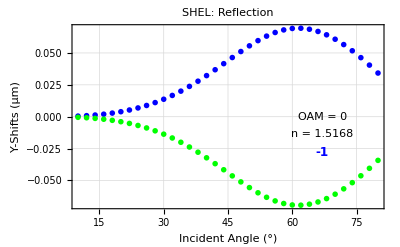

```mathematica
datminus=R4y$plotdata;
datplus=R3y$plotdata;

params$here = {wk->20000.,n->1.5168,θ->θloop Degree,k0->1,p->0,ℓ->0};

p$Ryspin=ListLinePlot[{datminus,datplus},PlotMarkers->{Graphics[Disk[]],.03},Joined->False,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{{Thickness[.006],Blue},{Thickness[.006],Green},Darker[Red]},FrameLabel->{font["Incident Angle (°)",14],font["Y-Shifts (μm)",14]},PlotLabel->font["SHEL: Reflection",16]];

vmax= Max[Transpose[datminus][[2]]];
vmin= Min[Transpose[datplus][[2]]];


p$Ryspinfinal = Show[p$Ryspin,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{67,vmin + 0.5 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{67,vmin + 0.4(vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font["-1",12],{67,vmin + 0.3 (vmax-vmin)}]},Background->White]
]
```

#### Bliokh’s Analytical Formula for Subcritical SHEL Shifts

From [Bliokh_PRE_2007.pdf] Eq 58 we have Bliokh’s expression for the shifts

-Graphics-

polarizations: s/TE/2/perpendicular    and p/TM/1/parallel
m_c … ±ⅈ

ρ_c^I = 1

ρ_c^R = R_2/R_1

ρ_c^T = T_2/T_1

```mathematica
ArcSin[1/n Sin[θ]]; (* Snell *)
```

```mathematica
R2=(Cos[θ]-√(n^2-Sin[θ]^2))/(Cos[θ]+√(n^2-Sin[θ]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(n^2 Cos[θ]-√(n^2-Sin[θ]^2))/(n^2 Cos[θ]+√(n^2-Sin[θ]^2));(* Fresnel Reflection Coefficient: p/TM *)

T1=(2 n)/(n^2+Sec[θ] √(n^2-Sin[θ]^2));

T2=(2 Cos[θ])/(Cos[θ]+√(n^2-Sin[θ]^2));
```

-Graphics-

```mathematica
(* mc = ⅈ for plus and -ⅈ for minus *)

Clear[mc];
kset = 2π/(632.8*10^-9);

ρcR =R2/R1;
θR = π-θ;
ΔR =Im[mc]/kset Cot[θ]((2ρcR Cos[θR]/Cos[θ]-1-ρcR^2)/(1+ρcR^2 Abs[mc]^2));

ρcT =T2/T1;
θT = ArcSin[1/n Sin[θ]];
ΔT =Im[mc]/kset Cot[θ]((2ρcT Cos[θT]/Cos[θ]-1-ρcT^2)/(1+ρcT^2 Abs[mc]^2));
```

```mathematica
θbrewster = ArcTan[n]/Degree /.params$here;
p$brewster=Graphics[{Magenta,Dashing->Tiny,Line[{{θbrewster,-100},{θbrewster,100}}]}];
```

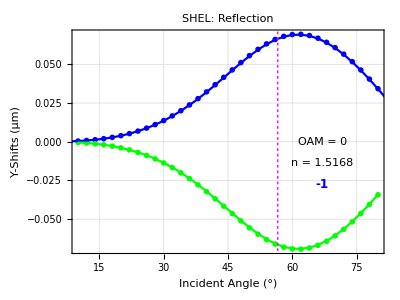

```mathematica
p$Rminus=ParametricPlot[{θ/Degree,10^6 ΔR /. {n->1.5168,mc->-ⅈ}},{θ,4 Degree,86 Degree},AspectRatio->.75,PlotStyle->Blue];

p$Rplus=ParametricPlot[{θ/Degree,10^6 ΔR /. {n->1.5168,mc->ⅈ}},{θ,10 Degree,80 Degree},AspectRatio->.75,PlotStyle->Green];

p$Rbliokh=Show[{p$Rminus,p$Rplus},PlotRange->All];

p$SHEL=Show[p$Ryspinfinal,p$Rbliokh,p$brewster,AspectRatio->0.75,BaseStyle->{"Tahoma",14}]
```

#### Plot Graphic For Manuscript

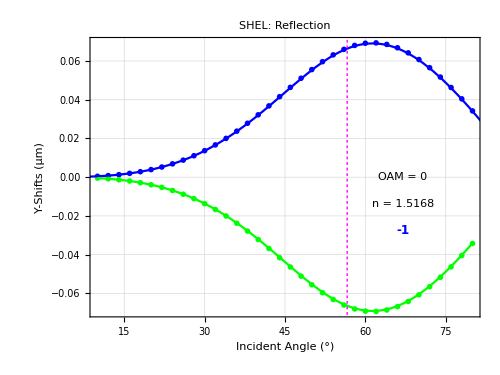

```mathematica
Show[p$SHEL,ImageSize->500]
```

### Centroid Shifts versus Angle of Incidence: n = 1.5168, OAM = 5 (Air/Glass) FIG 3

#### Analysis

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

```mathematica
θcrit = ArcSin[n]/Degree /. n->1/1.5168
```

41.2452

```mathematica
Clear[plots,k0];

fontset = 6;

IFshift$tab$R1 = {};
IFshift$tab$R2 = {};
IFshift$tab$R3 = {};
IFshift$tab$R4 = {};
IFshift$tab$T1 = {};
IFshift$tab$T2 = {};
IFshift$tab$T3 = {};
IFshift$tab$T4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1.5168,θ->θloop Degree,k0->1,p->0,ℓ->5};

Print["Angle of Incidence: ",θloop,"°"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)

Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eR = {(f[[1]]R1-f[[2]]κy Cot[θ](R1+R2)),f[[2]]R2 + f[[1]]κy Cot[θ](R1+R2 ),-(f[[1]]R1 κx + f[[2]]R2  κy)} /. params$here;

eRtab = Table[eR /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

IFshift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

IFshift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, IFshift$R1={IFshift$Rx,IFshift$Ry},f$flag==2,IFshift$R2={IFshift$Rx,IFshift$Ry},f$flag==3,IFshift$R3={IFshift$Rx,IFshift$Ry},f$flag==4,IFshift$R4={IFshift$Rx,IFshift$Ry}];
Which[f$flag ==1, IFshift$T1={IFshift$Tx,IFshift$Ty},f$flag==2,IFshift$T2={IFshift$Tx,IFshift$Ty},f$flag==3,IFshift$T3={IFshift$Tx,IFshift$Ty},f$flag==4,IFshift$T4={IFshift$Tx,IFshift$Ty}];

},{f$flag,1,4}];

AppendTo[IFshift$tab$R1 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R1}];
AppendTo[IFshift$tab$R2 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R2}];
AppendTo[IFshift$tab$R3 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R3}];
AppendTo[IFshift$tab$R4 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R4}];

Print["TM (Reflected) = ",IFshift$R1," μm"];
Print["TE (Reflected) = ",IFshift$R2," μm"];
Print["TM-TE (Reflected) = ",IFshift$R1-IFshift$R2," μm"];

(* Print["TM (Reflected) = ",IFshift$R3," μm"]; *)
Print["  "];

},{θloop,10.0,80.0,2.0}]
```

Angle of Incidence: 10.°

TM (Reflected) = {0,0.121917} μm

TE (Reflected) = {0,-0.116643} μm

TM-TE (Reflected) = {0,0.238561} μm

Angle of Incidence: 12.°

TM (Reflected) = {0,0.149323} μm

TE (Reflected) = {0,-0.140063} μm

TM-TE (Reflected) = {0,0.289386} μm

Angle of Incidence: 14.°

TM (Reflected) = {0,0.178518} μm

TE (Reflected) = {0,-0.163529} μm

TM-TE (Reflected) = {0,0.342047} μm

Angle of Incidence: 16.°

TM (Reflected) = {0,0.209931} μm

TE (Reflected) = {0,-0.187049} μm

TM-TE (Reflected) = {0,0.396979} μm

Angle of Incidence: 18.°

TM (Reflected) = {0,0.244062} μm

TE (Reflected) = {0,-0.210626} μm

TM-TE (Reflected) = {0,0.454688} μm

Angle of Incidence: 20.°

TM (Reflected) = {0,0.281509} μm

TE (Reflected) = {0,-0.234265} μm

TM-TE (Reflected) = {0,0.515774} μm

Angle of Incidence: 22.°

TM (Reflected) = {0,0.322995} μm

TE (Reflected) = {0,-0.257968} μm

TM-TE (Reflected) = {0,0.580963} μm

Angle of Incidence: 24.°

TM (Reflected) = {0,0.369413} μm

TE (Reflected) = {0,-0.281736} μm

TM-TE (Reflected) = {0,0.651148} μm

Angle of Incidence: 26.°

TM (Reflected) = {0,0.421877} μm

TE (Reflected) = {0,-0.305567} μm

TM-TE (Reflected) = {0,0.727444} μm

Angle of Incidence: 28.°

TM (Reflected) = {0,0.481808} μm

TE (Reflected) = {0,-0.329459} μm

TM-TE (Reflected) = {0,0.811267} μm

Angle of Incidence: 30.°

TM (Reflected) = {0,0.551046} μm

TE (Reflected) = {0,-0.353406} μm

TM-TE (Reflected) = {0,0.904451} μm

Angle of Incidence: 32.°

TM (Reflected) = {0,0.632023} μm

TE (Reflected) = {0,-0.377399} μm

TM-TE (Reflected) = {0,1.00942} μm

Angle of Incidence: 34.°

TM (Reflected) = {0,0.728031} μm

TE (Reflected) = {0,-0.401428} μm

TM-TE (Reflected) = {0,1.12946} μm

Angle of Incidence: 36.°

TM (Reflected) = {0,0.843634} μm

TE (Reflected) = {0,-0.425478} μm

TM-TE (Reflected) = {0,1.26911} μm

Angle of Incidence: 38.°

TM (Reflected) = {0,0.985356} μm

TE (Reflected) = {0,-0.44953} μm

TM-TE (Reflected) = {0,1.43489} μm

Angle of Incidence: 40.°

TM (Reflected) = {0,1.16287} μm

TE (Reflected) = {0,-0.473561} μm

TM-TE (Reflected) = {0,1.63643} μm

Angle of Incidence: 42.°

TM (Reflected) = {0,1.39113} μm

TE (Reflected) = {0,-0.497545} μm

TM-TE (Reflected) = {0,1.88868} μm

Angle of Incidence: 44.°

TM (Reflected) = {0,1.69462} μm

TE (Reflected) = {0,-0.521448} μm

TM-TE (Reflected) = {0,2.21607} μm

Angle of Incidence: 46.°

TM (Reflected) = {0,2.11627} μm

TE (Reflected) = {0,-0.545234} μm

TM-TE (Reflected) = {0,2.66151} μm

Angle of Incidence: 48.°

TM (Reflected) = {0,2.73895} μm

TE (Reflected) = {0,-0.568857} μm

TM-TE (Reflected) = {0,3.3078} μm

Angle of Incidence: 50.°

TM (Reflected) = {0,3.74591} μm

TE (Reflected) = {0,-0.592269} μm

TM-TE (Reflected) = {0,4.33818} μm

Angle of Incidence: 52.°

TM (Reflected) = {0,5.63893} μm

TE (Reflected) = {0,-0.615412} μm

TM-TE (Reflected) = {0,6.25434} μm

Angle of Incidence: 54.°

TM (Reflected) = {0,10.4614} μm

TE (Reflected) = {0,-0.638223} μm

TM-TE (Reflected) = {0,11.0996} μm

Angle of Incidence: 56.°

TM (Reflected) = {0,47.3232} μm

TE (Reflected) = {0,-0.660631} μm

TM-TE (Reflected) = {0,47.9838} μm

Angle of Incidence: 58.°

TM (Reflected) = {0,-21.4754} μm

TE (Reflected) = {0,-0.682557} μm

TM-TE (Reflected) = {0,-20.7928} μm

Angle of Incidence: 60.°

TM (Reflected) = {0,-9.26321} μm

TE (Reflected) = {0,-0.703918} μm

TM-TE (Reflected) = {0,-8.55929} μm

Angle of Incidence: 62.°

TM (Reflected) = {0,-6.11746} μm

TE (Reflected) = {0,-0.724621} μm

TM-TE (Reflected) = {0,-5.39284} μm

Angle of Incidence: 64.°

TM (Reflected) = {0,-4.68407} μm

TE (Reflected) = {0,-0.744568} μm

TM-TE (Reflected) = {0,-3.9395} μm

Angle of Incidence: 66.°

TM (Reflected) = {0,-3.8703} μm

TE (Reflected) = {0,-0.763657} μm

TM-TE (Reflected) = {0,-3.10664} μm

Angle of Incidence: 68.°

TM (Reflected) = {0,-3.35055} μm

TE (Reflected) = {0,-0.78178} μm

TM-TE (Reflected) = {0,-2.56877} μm

Angle of Incidence: 70.°

TM (Reflected) = {0,-2.99375} μm

TE (Reflected) = {0,-0.798826} μm

TM-TE (Reflected) = {0,-2.19493} μm

Angle of Incidence: 72.°

TM (Reflected) = {0,-2.73699} μm

TE (Reflected) = {0,-0.814684} μm

TM-TE (Reflected) = {0,-1.92231} μm

Angle of Incidence: 74.°

TM (Reflected) = {0,-2.54638} μm

TE (Reflected) = {0,-0.829242} μm

TM-TE (Reflected) = {0,-1.71714} μm

Angle of Incidence: 76.°

TM (Reflected) = {0,-2.4021} μm

TE (Reflected) = {0,-0.842391} μm

TM-TE (Reflected) = {0,-1.55971} μm

Angle of Incidence: 78.°

TM (Reflected) = {0,-2.29185} μm

TE (Reflected) = {0,-0.854028} μm

TM-TE (Reflected) = {0,-1.43782} μm

Angle of Incidence: 80.°

TM (Reflected) = {0,-2.20764} μm

TE (Reflected) = {0,-0.864056} μm

TM-TE (Reflected) = {0,-1.34358} μm

#### Data Record

```mathematica
shift$tab$R1={{5,10.,{0,0.12191735747768041}},{5,12.000000000000002,{0,0.1493229934620219}},{5,14.,{0,0.17851832093467496}},{5,16.,{0,0.20993087167077742}},{5,18.,{0,0.24406178130588152}},{5,20.,{0,0.28150850184531084}},{5,22.,{0,0.32299498714114616}},{5,24.000000000000004,{0,0.36941263449560985}},{5,26.,{0,0.4218769703116978}},{5,28.,{0,0.48180784052577647}},{5,29.999999999999996,{0,0.5510455260811113}},{5,32.,{0,0.6320232692346324}},{5,34.,{0,0.7280311892540245}},{5,36.,{0,0.8436337241855021}},{5,38.,{0,0.9853561676167144}},{5,40.,{0,1.1628672327771912}},{5,42.,{0,1.3911332035549464}},{5,44.,{0,1.6946229301951399}},{5,46.,{0,2.1162714134973957}},{5,48.00000000000001,{0,2.738945132678875}},{5,50.,{0,3.745912601668637}},{5,52.,{0,5.6389321461869875}},{5,54.,{0,10.461397511507599}},{5,56.,{0,47.32320445328254}},{5,58.00000000000001,{0,-21.47537030386604}},{5,59.99999999999999,{0,-9.263206862437642}},{5,62.,{0,-6.117460585810133}},{5,64.,{0,-4.684069235422199}},{5,66.,{0,-3.8702959866079154}},{5,68.,{0,-3.35055230300083}},{5,70.,{0,-2.9937516305202636}},{5,72.,{0,-2.7369934561151754}},{5,74.,{0,-2.5463844743718527}},{5,76.,{0,-2.402103096547561}},{5,78.,{0,-2.2918454657696836}},{5,80.,{0,-2.207638932625356}}};
```

```mathematica
shift$tab$R2={{5,10.,{0,-0.11664319789051154}},{5,12.000000000000002,{0,-0.14006255138658777}},{5,14.,{0,-0.16352905641802362}},{5,16.,{0,-0.18704857495826369}},{5,18.,{0,-0.2106259871171177}},{5,20.,{0,-0.23426500769253444}},{5,22.,{0,-0.25796798500385615}},{5,24.000000000000004,{0,-0.2817356804894575}},{5,26.,{0,-0.30556702707651007}},{5,28.,{0,-0.3294588638268222}},{5,29.999999999999996,{0,-0.3534056464637363}},{5,32.,{0,-0.3773991323374137}},{5,34.,{0,-0.40142803925029263}},{5,36.,{0,-0.4254776793964701}},{5,38.,{0,-0.4495295696458567}},{5,40.,{0,-0.47356102148781515}},{5,42.,{0,-0.49754471516838855}},{5,44.,{0,-0.5214482658012415}},{5,46.,{0,-0.5452337901484108}},{5,48.00000000000001,{0,-0.5688574874499269}},{5,50.,{0,-0.592269249095405}},{5,52.,{0,-0.6154123175926267}},{5,54.,{0,-0.638223016759418}},{5,56.,{0,-0.6606305804121806}},{5,58.00000000000001,{0,-0.682557108478921}},{5,59.99999999999999,{0,-0.7039176828365804}},{5,62.,{0,-0.7246206752354424}},{5,64.,{0,-0.7445682791352561}},{5,66.,{0,-0.7636572935450879}},{5,68.,{0,-0.7817801811138034}},{5,70.,{0,-0.7988264119782037}},{5,72.,{0,-0.814684092790598}},{5,74.,{0,-0.8292418627664789}},{5,76.,{0,-0.8423910210232911}},{5,78.,{0,-0.8540278276179449}},{5,80.,{0,-0.8640559026859658}}};
```

```mathematica
shift$tab$R3={{5,10.,{0,-0.0017346489026712976}},{5,12.000000000000002,{0,-0.0030509831127771845}},{5,14.,{0,-0.00494614795931107}},{5,16.,{0,-0.007559290558891951}},{5,18.,{0,-0.01105008625329325}},{5,20.,{0,-0.015601980537587493}},{5,22.,{0,-0.02142524208997429}},{5,24.000000000000004,{0,-0.02875955592156893}},{5,26.,{0,-0.03787576336942831}},{5,28.,{0,-0.04907620881278171}},{5,29.999999999999996,{0,-0.06269299136174662}},{5,32.,{0,-0.07908327063454598}},{5,34.,{0,-0.09862067553085091}},{5,36.,{0,-0.12168187707997884}},{5,38.,{0,-0.14862759777109444}},{5,40.,{0,-0.17977782438547968}},{5,42.,{0,-0.21538184733579482}},{5,44.,{0,-0.25558496323874486}},{5,46.,{0,-0.30039512970212734}},{5,48.00000000000001,{0,-0.3496542558206103}},{5,50.,{0,-0.40301969076470934}},{5,52.,{0,-0.459961318727796}},{5,54.,{0,-0.5197781095982407}},{5,56.,{0,-0.5816350232019083}},{5,58.00000000000001,{0,-0.6446173776337027}},{5,59.99999999999999,{0,-0.7077961797369584}},{5,62.,{0,-0.7702956080366702}},{5,64.,{0,-0.831353595090583}},{5,66.,{0,-0.8903683356791111}},{5,68.,{0,-0.9469268798711166}},{5,70.,{0,-1.0008156811995736}},{5,72.,{0,-1.0520160560832577}},{5,74.,{0,-1.1006893614688626}},{5,76.,{0,-1.1471572329618966}},{5,78.,{0,-1.1918817391109102}},{5,80.,{0,-1.2354492751467498}}};
```

```mathematica
shift$tab$R4={{5,10.,{0,-0.0026823413210227253}},{5,12.000000000000002,{0,-0.004697444605017907}},{5,14.,{0,-0.007576809749962235}},{5,16.,{0,-0.011512915736427822}},{5,18.,{0,-0.016720659113975855}},{5,20.,{0,-0.023440200425597538}},{5,22.,{0,-0.031939246209984444}},{5,24.000000000000004,{0,-0.04251438378144514}},{5,26.,{0,-0.05549094914535062}},{5,28.,{0,-0.07122075460794641}},{5,29.999999999999996,{0,-0.09007685252142596}},{5,32.,{0,-0.1124444028037136}},{5,34.,{0,-0.1387066912170199}},{5,36.,{0,-0.16922549816352128}},{5,38.,{0,-0.20431542571184635}},{5,40.,{0,-0.2442125496649467}},{5,42.,{0,-0.28903890685975636}},{5,44.,{0,-0.33876580395912903}},{5,46.,{0,-0.39318052120955616}},{5,48.00000000000001,{0,-0.4518622728175143}},{5,50.,{0,-0.5141737249421704}},{5,52.,{0,-0.5792734172309999}},{5,54.,{0,-0.6461518211532238}},{5,56.,{0,-0.7136897569988907}},{5,58.00000000000001,{0,-0.7807333640060766}},{5,59.99999999999999,{0,-0.8461760886708237}},{5,62.,{0,-0.9090364545493673}},{5,64.,{0,-0.9685213396734218}},{5,66.,{0,-1.024067806014582}},{5,68.,{0,-1.0753611214405494}},{5,70.,{0,-1.1223310968876923}},{5,72.,{0,-1.165132112058621}},{5,74.,{0,-1.204113717214262}},{5,76.,{0,-1.2397886001618714}},{5,78.,{0,-1.272803523370818}},{5,80.,{0,-1.303917205465878}}};
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];

RΔx$plotdata = Table[{R1x$plotdata[[i,1]],R1x$plotdata[[i,2]]-R2x$plotdata[[i,2]]},{i,1,Length[R1x$plotdata]}];

RΔy$plotdata = Table[{R1y$plotdata[[i,1]],R1y$plotdata[[i,2]]-R2y$plotdata[[i,2]]},{i,1,Length[R1y$plotdata]}];
```

#### Reflection Plots

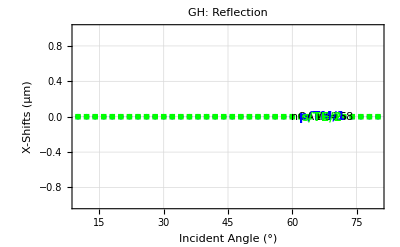

```mathematica
params$here = {wk->20000.,n->1.5168,θ->θloop Degree,k0->1,p->0,ℓ->5};

dat=Join[R1x$plotdata,R2x$plotdata];

p$Rxspin=ListLinePlot[{R1x$plotdata,R2x$plotdata},PlotMarkers->{{Graphics[Disk[]],.03},{Graphics[Rectangle[]],.02}},Joined->False,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{{Thickness[.006],Blue},{Thickness[.006],Green},Darker[Red]},FrameLabel->{font["Incident Angle (°)",14],font["X-Shifts (μm)",14]},PlotLabel->font["GH: Reflection",16]];

vmax= Max[Transpose[dat][[2]]];
vmin= Min[Transpose[dat][[2]]];


p$Rxspinfinal = Show[p$Rxspin,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{67,vmin + 0.5 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{67,vmin + 0.4(vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font["p/TM/1",12],{67,vmin + 0.3(vmax-vmin)}]},Background->White],
Graphics[{Green,Text[font["s/TE/2",12],{67,vmin + 0.2(vmax-vmin)}]},Background->White]
]
```

```mathematica
θbrewster = ArcTan[n]/Degree /.params$here;
p$brewster=Graphics[{Magenta,Dashing->Tiny,Line[{{θbrewster,-100},{θbrewster,100}}]}];

θcrit = ArcSin[n]/Degree /.params$here;
p$crit=Graphics[{Magenta,Dashing->Tiny,Line[{{θcrit,-100},{θcrit,100}}]}];
```

TM - TE, Y-Shift

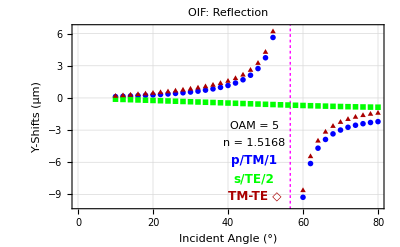

```mathematica
dat=Join[R1y$plotdata,R2y$plotdata];
vmax= 6.5;
vmin= -10;

p$RyTETM=ListLinePlot[{R1y$plotdata,R2y$plotdata,RΔy$plotdata},PlotMarkers->{{Graphics[Disk[]],.03},{Graphics[Rectangle[]],.02},{Graphics[Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]],.03}},Joined->False,GridLines->Automatic,Frame->True,PlotRange->{vmin,vmax},PlotStyle->{{Thickness[.006],Blue},{Thickness[.006],Green},Darker[Red]},FrameLabel->{font["Incident Angle (°)",14],font["Y-Shifts (μm)",14]},PlotLabel->font["OIF: Reflection",16]];

p$RyTETMfinal = Show[p$RyTETM,p$brewster,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{47,vmin + 0.45 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{47,vmin + 0.35(vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font["p/TM/1",12],{47,vmin + 0.25(vmax-vmin)}]},Background->White],
Graphics[{Green,Text[font["s/TE/2",12],{47,vmin + 0.15(vmax-vmin)}]},Background->White],
Graphics[{Darker[Red],Text[font["TM-TE ◇",12],{47,vmin + 0.05 (vmax-vmin)}]},Background->White]
]
```

Spins, y-Shift

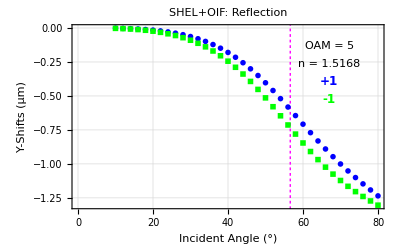

```mathematica
dat=Join[R3y$plotdata,R4y$plotdata];
vmax= Max[Transpose[dat][[2]]];
vmin= Min[Transpose[dat][[2]]];

p$Ryspin=ListLinePlot[{R3y$plotdata,R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.03},{Graphics[Rectangle[]],.02},{Graphics[Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]],.03}},Joined->False,GridLines->Automatic,Frame->True,PlotRange->{vmin,vmax},PlotStyle->{{Thickness[.006],Blue},{Thickness[.006],Green},Darker[Red]},FrameLabel->{font["Incident Angle (°)",14],font["Y-Shifts (μm)",14]},PlotLabel->font["SHEL+OIF: Reflection",16]];



p$Ryspinfinal = Show[p$Ryspin,p$brewster,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{67,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{67,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font["+1",12],{67,vmin + 0.7(vmax-vmin)}]},Background->White],
Graphics[{Green,Text[font["-1",12],{67,vmin + 0.6(vmax-vmin)}]},Background->White]
]
```

#### Dasgupta’s Experimental Data for OAM = 5

Here is experimental data, obtained using Data Thirf, associated with the OIF shift of LG beams as a function of angle of incidence. The data was taken from the experimental measurements shown below. This is Figure 4 of Dasgupta, P.K. Gupta / Optics Communications 257 (2006) 91–96 [IF_Measurement_Dasgupta_OptComm_2006.pdf]. 

This is used in the following analysis:  n = 1.5, OAM = 5, 4 mm Beam. I will eventually re-run this analysis with n = 1.5168 (BK7).

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];

exptdata = Drop[Import["IF_Expt_Data_Dasgupta_for_Mathematica.txt","Table"],1];

temp = Table[{exptdata[[i,1]],exptdata[[i,2]]/1000.},{i,1,Length[exptdata]}];

exptdata = temp
```

{{27.069,0.784726},{30.0862,0.995099},{33.1034,1.10047},{36.1207,1.18484},{38.9655,1.5737},{41.8103,1.9888},{71.9828,-1.89248},{75,-1.6716},{78.0172,-1.48223},{81.0345,-1.20886}}

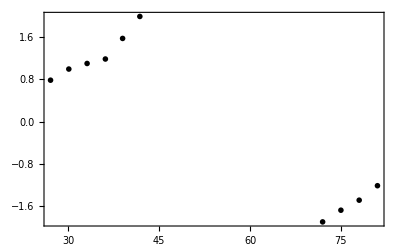

```mathematica
p$dasgupta=ListLinePlot[exptdata,Joined->False,Frame->True,PlotStyle->{Black},PlotMarkers->{Graphics[Disk[]],.04},PlotRange->All]
```

```mathematica
k0set= (2 π)/(632.8*10^-9);

thicknesstab = Table[{L, ToString[0.1Round[10L/k0set*10^6]]},{L,10,100,10}];

thicknesstab = PrependTo[thicknesstab,{"Lk_0  ","Air Gap (μm)"}];

TableForm[thicknesstab]
```

Lk_0   | Air Gap (μm)
10 | 1.
20 | 2.
30 | 3.
40 | 4.
50 | 5.
60 | 6.
70 | 7.
80 | 8.1
90 | 9.1
100 | 10.1

For purely Gaussian beams, there is no OAM but there is still an IF shift. This was measured by in OPTICS LETTERS / Vol. 39, No. 15 / August 1, 2014 [IF_GH_Measurement_ Prajapati_Opt_Lett_2014.pdf] with the key result shown in panel (b) below. This is for a glass-to-air interface with n = 1/1.5168 and He-Ne laser (632.8 nm). The critical angle is 41.8°.

-Graphics-

#### Prajapati’s Experimental SHEL Data

```mathematica
SetDirectory[NotebookDirectory[]];

exptdata$SHEL$plus = Drop[Import["Prajapati_Spin_Plus_SHEL_Expt_Data.txt","Table"],0];
exptdata$SHEL$minus = Drop[Import["Prajapati_Spin_Minus_SHEL_Expt_Data.txt","Table"],0];
```

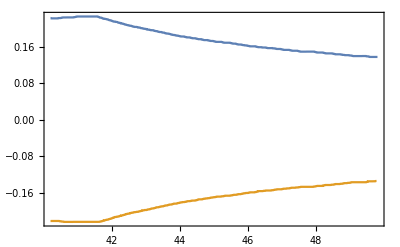

```mathematica
p$prajapati=ListLinePlot[{exptdata$SHEL$plus,exptdata$SHEL$minus},Joined->True,Frame->True,PlotRange->All]
```

#### Bliokh’s Analytical Formula for Subcritical SHEL Shifts

From [Bliokh_PRE_2007.pdf] Eq 58 we have Bliokh’s expression for the shifts

-Graphics-

polarizations: s/TE/2/perpendicular    and p/TM/1/parallel
m_c … ±ⅈ

ρ_c^I = 1

ρ_c^R = R_2/R_1

ρ_c^T = T_2/T_1

```mathematica
Clear[R1play,R2play];

ArcSin[1/n Sin[θ]]; (* Snell *)

R1play=(n^2 Cos[θ]-√(n^2-Sin[θ]^2))/(n^2 Cos[θ]+√(n^2-Sin[θ]^2));(* Fresnel Reflection Coefficient: p/TM *)

R2play=(Cos[θ]-√(n^2-Sin[θ]^2))/(Cos[θ]+√(n^2-Sin[θ]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)
```

-Graphics-

```mathematica
(* mc = ⅈ for minus and -ⅈ for plus *)

Clear[mc];
kset = 2π/(632.8*10^-9);

ρcR =R2play/R1play;
θR = π-θ;
ΔR =Im[mc]/kset Cot[θ]((2ρcR Cos[θR]/Cos[θ]-1-ρcR^2)/(1+ρcR^2 Abs[mc]^2));

ρcT =T2/T1;
θT = ArcSin[1/n Sin[θ]];
ΔT =Im[mc]/kset Cot[θ]((2ρcT Cos[θT]/Cos[θ]-1-ρcT^2)/(1+ρcT^2 Abs[mc]^2));
```

```mathematica
θbrewster = ArcTan[n]/Degree /.params$here;
p$brewster=Graphics[{Magenta,Dashing->Tiny,Line[{{θbrewster,-100},{θbrewster,100}}]}];
```

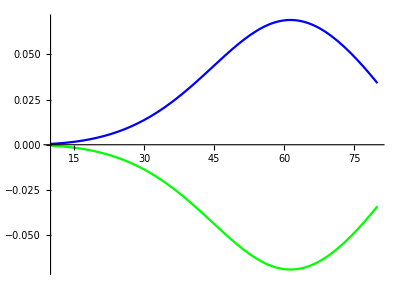

```mathematica
p$Rplus=ParametricPlot[{θ/Degree,10^6 ΔR /. {n->1.5168,mc->-ⅈ}},{θ,10 Degree,80 Degree},AspectRatio->.75,PlotStyle->Blue];

p$Rminus=ParametricPlot[{θ/Degree,10^6 ΔR /. {n->1.5168,mc->ⅈ}},{θ,10 Degree,80 Degree},AspectRatio->.75,PlotStyle->Green];

p$Rbliokh=Show[{p$Rplus,p$Rminus},PlotRange->All]
```

#### Plot Graphic For Manuscript

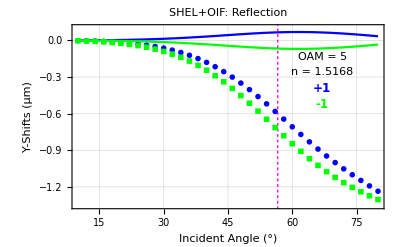

```mathematica
Show[p$Ryspinfinal,p$Rbliokh,PlotRange->{{10,80},{-1.35,0.1}}]
```

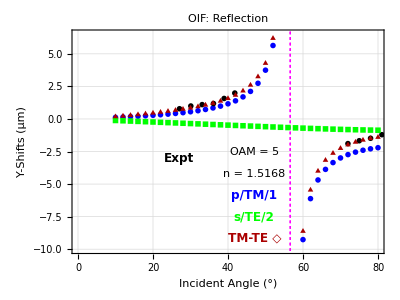

```mathematica
p$OIFplusSHEL=Show[{p$RyTETMfinal,p$dasgupta,p$brewster,Graphics[{Black,Text[font["Expt",12],{27,-3}]},Background->White]},AspectRatio->0.75]
```

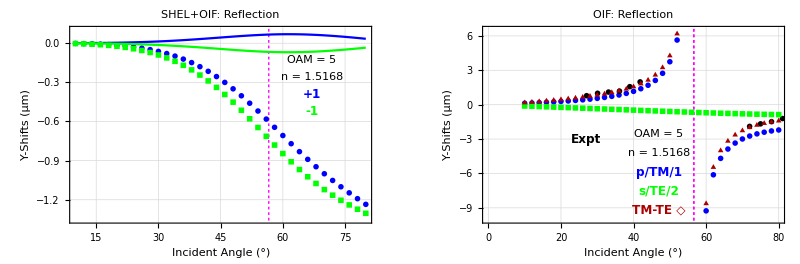

```mathematica
GraphicsRow[{Show[p$Ryspinfinal,p$Rbliokh,PlotRange->{{10,80},{-1.35,0.1}}],p$OIFplusSHEL},ImageSize->800]
```

### Centroid Shifts versus Angle of Incidence: n = 1/1.5168, OAM = 0 (Glass/Air) FIG 4

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.5
```

33.6901

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

```mathematica
θcrit = ArcSin[n]/Degree /. n->1/1.5
```

41.8103

#### Analysis

```mathematica
Clear[plots,k0];

fontset = 6;

IFshift$tab$R1 = {};
IFshift$tab$R2 = {};
IFshift$tab$R3 = {};
IFshift$tab$R4 = {};
IFshift$tab$T1 = {};
IFshift$tab$T2 = {};
IFshift$tab$T3 = {};
IFshift$tab$T4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1/1.5168,θ->θloop Degree,k0->1,p->0,ℓ->0};

Print["Angle of Incidence: ",θloop,"°"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)

Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eR = {(f[[1]]R1-f[[2]]κy Cot[θ](R1+R2)),f[[2]]R2 + f[[1]]κy Cot[θ](R1+R2 ),-(f[[1]]R1 κx + f[[2]]R2  κy)} /. params$here;

eRtab = Table[eR /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

IFshift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

IFshift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, IFshift$R1={IFshift$Rx,IFshift$Ry},f$flag==2,IFshift$R2={IFshift$Rx,IFshift$Ry},f$flag==3,IFshift$R3={IFshift$Rx,IFshift$Ry},f$flag==4,IFshift$R4={IFshift$Rx,IFshift$Ry}];
Which[f$flag ==1, IFshift$T1={IFshift$Tx,IFshift$Ty},f$flag==2,IFshift$T2={IFshift$Tx,IFshift$Ty},f$flag==3,IFshift$T3={IFshift$Tx,IFshift$Ty},f$flag==4,IFshift$T4={IFshift$Tx,IFshift$Ty}];

},{f$flag,1,4}];

AppendTo[IFshift$tab$R1 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R1}];
AppendTo[IFshift$tab$R2 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R2}];
AppendTo[IFshift$tab$R3 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R3}];
AppendTo[IFshift$tab$R4 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R4}];

Print["TE x (Reflected) = ",IFshift$R1," μm"]; 
Print["  "];

},{θloop,10.0,80.0,2.0}]
```

Angle of Incidence: 10.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 12.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 14.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 16.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 18.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 20.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 22.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 24.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 26.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 28.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 30.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 32.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 34.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 36.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 38.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 40.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 42.°

TE x (Reflected) = {-2.47845,0} μm

Angle of Incidence: 44.°

TE x (Reflected) = {-1.08401,0} μm

Angle of Incidence: 46.°

TE x (Reflected) = {-0.714854,0} μm

Angle of Incidence: 48.°

TE x (Reflected) = {-0.533105,0} μm

Angle of Incidence: 50.°

TE x (Reflected) = {-0.424296,0} μm

Angle of Incidence: 52.°

TE x (Reflected) = {-0.35211,0} μm

Angle of Incidence: 54.°

TE x (Reflected) = {-0.301018,0} μm

Angle of Incidence: 56.°

TE x (Reflected) = {-0.263198,0} μm

Angle of Incidence: 58.°

TE x (Reflected) = {-0.234268,0} μm

Angle of Incidence: 60.°

TE x (Reflected) = {-0.211581,0} μm

Angle of Incidence: 62.°

TE x (Reflected) = {-0.193446,0} μm

Angle of Incidence: 64.°

TE x (Reflected) = {-0.178734,0} μm

Angle of Incidence: 66.°

TE x (Reflected) = {-0.166665,0} μm

Angle of Incidence: 68.°

TE x (Reflected) = {-0.156682,0} μm

Angle of Incidence: 70.°

TE x (Reflected) = {-0.148381,0} μm

Angle of Incidence: 72.°

TE x (Reflected) = {-0.141462,0} μm

Angle of Incidence: 74.°

TE x (Reflected) = {-0.135697,0} μm

Angle of Incidence: 76.°

TE x (Reflected) = {-0.130916,0} μm

Angle of Incidence: 78.°

TE x (Reflected) = {-0.126984,0} μm

Angle of Incidence: 80.°

TE x (Reflected) = {-0.123802,0} μm

#### Data Record

```mathematica
IFshift$tab$R4
```

IFshift$tab$R4

```mathematica
shift$tab$R1={{0,10.,{0,0}},{0,12.000000000000002,{0,0}},{0,14.,{0,0}},{0,16.,{0,0}},{0,18.,{0,0}},{0,20.,{0,0}},{0,22.,{0,0}},{0,24.000000000000004,{0,0}},{0,26.,{0,0}},{0,28.,{0,0}},{0,29.999999999999996,{0,0}},{0,32.,{0,0}},{0,34.,{0,0}},{0,36.,{0,0}},{0,38.,{0,0}},{0,40.,{0,0}},{0,42.,{-2.4784549739672106,0}},{0,44.,{-1.084011849773767,0}},{0,46.,{-0.7148538442780695,0}},{0,48.00000000000001,{-0.5331053210348243,0}},{0,50.,{-0.42429617485207943,0}},{0,52.,{-0.35210992735964475,0}},{0,54.,{-0.3010182586139609,0}},{0,56.,{-0.26319837378938005,0}},{0,58.00000000000001,{-0.23426812456628376,0}},{0,59.99999999999999,{-0.21158104839033343,0}},{0,62.,{-0.19344614824890938,0}},{0,64.,{-0.178734366165305,0}},{0,66.,{-0.16666486587822277,0}},{0,68.,{-0.15668199516321035,0}},{0,70.,{-0.14838102135482734,0}},{0,72.,{-0.14146152000001655,0}},{0,74.,{-0.13569714843101316,0}},{0,76.,{-0.13091550110750805,0}},{0,78.,{-0.12698437706511256,0}},{0,80.,{-0.12380224882282513,0}}};
```

```mathematica
shift$tab$R2={{0,10.,{0,0}},{0,12.000000000000002,{0,0}},{0,14.,{0,0}},{0,16.,{0,0}},{0,18.,{0,0}},{0,20.,{0,0}},{0,22.,{0,0}},{0,24.000000000000004,{0,0}},{0,26.,{0,0}},{0,28.,{0,0}},{0,29.999999999999996,{0,0}},{0,32.,{0,0}},{0,34.,{0,0}},{0,36.,{0,0}},{0,38.,{0,0}},{0,40.,{0,0}},{0,42.,{-1.1842879378726336,0}},{0,44.,{-0.6425425265838541,0}},{0,46.,{-0.5060715711920085,0}},{0,48.00000000000001,{-0.43866501211043757,0}},{0,50.,{-0.3975314882541826,0}},{0,52.,{-0.369572725412535,0}},{0,54.,{-0.3492788722550321,0}},{0,56.,{-0.33388549669244044,0}},{0,58.00000000000001,{-0.32183825777657565,0}},{0,59.99999999999999,{-0.31219030318166074,0}},{0,62.,{-0.30432950776362533,0}},{0,64.,{-0.29784161604267984,0}},{0,66.,{-0.29243598302672597,0}},{0,68.,{-0.28790272045047016,0}},{0,70.,{-0.2840867051433418,0}},{0,72.,{-0.28087115743633956,0}},{0,74.,{-0.2781669078607521,0}},{0,76.,{-0.27590518150267423,0}},{0,78.,{-0.27403263400072825,0}},{0,80.,{-0.2725078748460959,0}}};
```

```mathematica
shift$tab$R3={{0,10.,{0,0.0026547173294844757}},{0,12.000000000000002,{0,0.004728284287551314}},{0,14.,{0,0.007778367923518495}},{0,16.,{0,0.012085152656016798}},{0,18.,{0,0.01798437031543145}},{0,20.,{0,0.02586919496072717}},{0,22.,{0,0.03617995095537794}},{0,24.000000000000004,{0,0.04937044405222336}},{0,26.,{0,0.0658350426816069}},{0,28.,{0,0.08577958712827141}},{0,29.999999999999996,{0,0.10903058977987982}},{0,32.,{0,0.1348133624382743}},{0,34.,{0,0.16159371548259874}},{0,36.,{0,0.1871353206421946}},{0,38.,{0,0.208891438691909}},{0,40.,{0,0.22466430983347221}},{0,42.,{-1.8313714559256469,0.21700456230133822}},{0,44.,{-0.8632771881931228,0.1894607634398401}},{0,46.,{-0.6104627077436263,0.1701054056723896}},{0,48.00000000000001,{-0.4858851665812183,0.15543562390666504}},{0,50.,{-0.4109138315445437,0.143636976973174}},{0,52.,{-0.36084132639181477,0.13367680308705757}},{0,54.,{-0.32514856543449655,0.12492559530469827}},{0,56.,{-0.2985419352208732,0.11697935621912973}},{0,58.00000000000001,{-0.27805319118860433,0.10956856661549023}},{0,59.99999999999999,{-0.26188567579744687,0.10250818538728965}},{0,62.,{-0.24888782804061668,0.09566859301253736}},{0,64.,{-0.23828799109254262,0.08895789547516486}},{0,66.,{-0.2295504244753739,0.08231070634075165}},{0,68.,{-0.22229235783260223,0.07568078304833287}},{0,70.,{-0.21623386324908453,0.06903604050664355}},{0,72.,{-0.21116633872104051,0.062355075865446516}},{0,74.,{-0.20693202814015774,0.05562468183716136}},{0,76.,{-0.20341034129077892,0.04883801945658598}},{0,78.,{-0.20050850553578284,0.041993241131474505}},{0,80.,{-0.19815506183732295,0.03509242492650682}}};
```

```mathematica
shift$tab$R4={{0,10.,{0,-0.0026547173867333294}},{0,12.000000000000002,{0,-0.004728284316175741}},{0,14.,{0,-0.007778367952142921}},{0,16.,{0,-0.012085152684641226}},{0,18.,{0,-0.01798437033260611}},{0,20.,{0,-0.02586919503515068}},{0,22.,{0,-0.036179950966827704}},{0,24.000000000000004,{0,-0.04937044413237175}},{0,26.,{0,-0.06583504274458064}},{0,28.,{0,-0.08577958723131934}},{0,29.999999999999996,{0,-0.10903058981995403}},{0,32.,{0,-0.13481336249552314}},{0,34.,{0,-0.16159371551694804}},{0,36.,{0,-0.18713532067081903}},{0,38.,{0,-0.20889143881213157}},{0,40.,{0,-0.22466430989072103}},{0,42.,{-1.8313714558855727,-0.21700456236431198}},{0,44.,{-0.8632771881873978,-0.18946076349136406}},{0,46.,{-0.6104627077436263,-0.17010540575826288}},{0,48.00000000000001,{-0.4858851665812183,-0.1554356239639139}},{0,50.,{-0.4109138315445437,-0.14363697702469796}},{0,52.,{-0.36084132639181477,-0.1336768031843806}},{0,54.,{-0.32514856543449655,-0.12492559542492086}},{0,56.,{-0.2985419352208732,-0.11697935624775416}},{0,58.00000000000001,{-0.2780531911714297,-0.10956856667846397}},{0,59.99999999999999,{-0.2618856757802722,-0.10250818545026338}},{0,62.,{-0.24888782801199225,-0.09566859310413553}},{0,64.,{-0.23828799108681775,-0.08895789556103814}},{0,66.,{-0.22955042448682367,-0.08231070642662493}},{0,68.,{-0.22229235783260223,-0.07568078317428036}},{0,70.,{-0.21623386324335964,-0.06903604056961729}},{0,72.,{-0.21116633870959076,-0.06235507595704468}},{0,74.,{-0.2069320281516075,-0.05562468189441022}},{0,76.,{-0.20341034131367847,-0.04883801955963392}},{0,78.,{-0.20050850553578284,-0.041993241217347786}},{0,80.,{-0.19815506184304785,-0.03509242498948056}}};
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### Reflection Plots

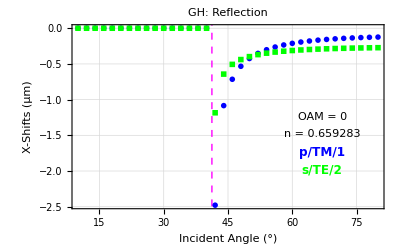

```mathematica
params$here = {wk->20000.,n->1/1.5168,θ->θloop Degree,k0->1,p->0,ℓ->0};

dat=Join[R1x$plotdata,R2x$plotdata];

p$Rxspin=ListLinePlot[{R1x$plotdata,R2x$plotdata},PlotMarkers->{{Graphics[Disk[]],.03},{Graphics[Rectangle[]],.02}},Joined->False,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{{Thickness[.006],Blue},{Thickness[.006],Green},Darker[Red]},FrameLabel->{font["Incident Angle (°)",14],font["X-Shifts (μm)",14]},PlotLabel->font["GH: Reflection",16]];

vmax= Max[Transpose[dat][[2]]];
vmin= Min[Transpose[dat][[2]]];


θcrit = ArcSin[n]/Degree /.params$here;
p$crit=Graphics[{Magenta,Dashing->Small,Line[{{θcrit,-5},{θcrit,5}}]}];


p$Rxspinfinal = Show[p$Rxspin,p$crit,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{67,vmin + 0.5 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{67,vmin + 0.4(vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font["p/TM/1",12],{67,vmin + 0.3(vmax-vmin)}]},Background->White],
Graphics[{Green,Text[font["s/TE/2",12],{67,vmin + 0.2(vmax-vmin)}]},Background->White]
]
```

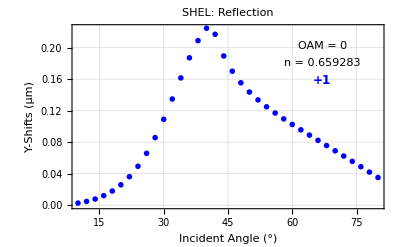

```mathematica
dat=R3y$plotdata;

p$Ryspin=ListLinePlot[dat,PlotMarkers->{Graphics[Disk[]],.03},Joined->False,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{{Thickness[.006],Blue},{Thickness[.006],Green},Darker[Red]},FrameLabel->{font["Incident Angle (°)",14],font["Y-Shifts (μm)",14]},PlotLabel->font["SHEL: Reflection",16]];

vmax= Max[Transpose[dat][[2]]];
vmin= Min[Transpose[dat][[2]]];


p$Ryspinfinal = Show[p$Ryspin,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{67,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{67,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font["+1",12],{67,vmin + 0.7(vmax-vmin)}]},Background->White]
]
```

#### Construction of Artmann Formula for the Goos-Hanchen Shifts

The work below does not derive Artmann’s formula for the GH shift. Rather, Artmann’s formula is used to get an explicit expression for the GH shift. However, in the application section in which a Gaussian beam is considered analytically, I derive Artmann’s formula explicitly by analytically calculating the centroid of the reflected beam. (That was fun and cool to do!)

Start by defining the two reflection coefficients. These will be complex valued for angles of incidence greater than the critical angle. The existence of a critical angle implies that n_2 < n_1--i.e. that the wave impinges on a material with a lower dielectric constant.

```mathematica
Clear[R1$Art,R2$Art,β$Art,n];

R2$Art=(Cos[β$Art]-√(n^2-Sin[β$Art]^2))/(Cos[β$Art]+√(n^2-Sin[β$Art]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1$Art=(-n^2 Cos[β$Art]+√(n^2-Sin[β$Art]^2))/(n^2 Cos[β$Art]+√(n^2-Sin[β$Art]^2));(* Fresnel Reflection Coefficient: p/TM *)
```

The GH shift can be estimated from the phase of these reflection coefficients. These phases, in turn, can be obtained in an analytically simple form or just by brute force. The approaches are shown to be equivalent below.

The brute force approach is:

```mathematica
Clear[Φ1,Φ2];

Φ1[β$Art_,n_]=FullSimplify[ArcTan[Re[R1],Im[R1]]];

Φ2[β$Art_,n_]=FullSimplify[ArcTan[Re[R2 ],Im[R2]]];
```

The derivative of these expressions with respect to β gives the GH shift:

GH_λ := (∂_β Φ_λ)/k_0

This is written in the coordinate system of the reflected beam, and the shift will come out to be negative. This is still “up and to the right” in our fixed frame though. If we use the expressions for Φ directly, the resulting formulae are ugly and do not offer any insights. We can analytically derive equivalent phase representations, with only a little effort, that work much better. First separate the reflection coefficients into real and imaginary parts.

```mathematica
((-n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2))/(n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2)))((n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2))/(n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2)))
```

(-n^2 (√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])+ⅈ √(1-n^2-(√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])^2))/(n^2 (√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])+ⅈ √(1-n^2-(√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])^2))

```mathematica
((-n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2))(n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2))
```

1/(-n^2+n^4 Cos[θ]^2+Sin[θ]^2)(n^2 (√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])-ⅈ √(1-n^2-(√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])^2)) (-n^2 (√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])+ⅈ √(1-n^2-(√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])^2))

```mathematica
R1$analytic=(-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2)+ⅈ 2 n^2 Cos[β] √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2);
```

```mathematica
R2$analytic=((Cos[θ])^2-2ⅈ Cos[θ] √(1-n^2-Cos[θ]^2)-(1-n^2-Cos[θ]^2))/((Cos[θ])^2+1-n^2-Cos[θ]^2);
```

Then the phases are

```mathematica
Clear[Φ1$analytic];
Φ1$analytic[θ_,n_]=FullSimplify[ArcTan[-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2),2 n^2 Cos[θ] √(Sin[θ]^2-n^2)] ,{θ>0,n>0,(Sin[θ]^2-n^2)>0}]
```

ArcTan[-n^2-n^4 Cos[θ]^2+Sin[θ]^2,2 n^2 Cos[θ] √(-n^2+Sin[θ]^2)]

```mathematica
Clear[Φ2$analytic];
Φ2$analytic[θ_,n_]=FullSimplify[ArcTan[(Cos[θ])^2-(1-n^2-Cos[θ]^2),-2Cos[θ] √(1-n^2-Cos[θ]^2)] ,{θ>0,n>0,1-n^2-Cos[θ]^2>0}]
```

ArcTan[n^2+Cos[2 θ],-2 Cos[θ] √(1-n^2-Cos[θ]^2)]

Below is a comparison of the two expressions for Φ_1. They are clearly equivalent.

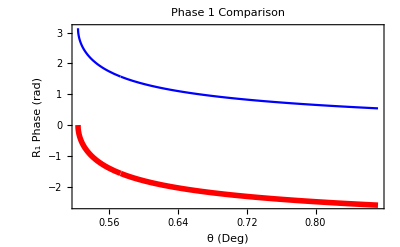

```mathematica
Plot[{Φ1[θ,1/2],Φ1$analytic[θ,1/2]},{θ,30 Degree, 50 Degree},PlotStyle->{{Thickness[.01],Red},Blue},Frame->True,FrameLabel->{font["θ (Deg)",10],font["R_1 Phase (rad)",10]},PlotLabel->font["Phase 1 Comparison",14]]
```

Below is a comparison of the two expressions for Φ_2. They are clearly equivalent.

```mathematica
Plot[{Φ2[θ,1/2],Φ2$analytic[θ,1/2]},{θ,30 Degree, 50 Degree},PlotStyle->{{Thickness[.01],Red},Blue},Frame->True,FrameLabel->{font["θ (Deg)",10],font["R_2 Phase (rad)",10]},PlotLabel->font["Phase 2 Comparison",14]]
```

-Graphics-

These formula can be used to calculate the GH shifts for each polarization using Artmann’s formulae:

```mathematica
Clear[GHshift$1,GHshift$2,k0];
GHshift$1[θ_,n_]=1/k0 FullSimplify[D[Φ1$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]

GHshift$2[θ_,n_]=1/k0 FullSimplify[D[Φ2$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]
```

(4 n^2 Sin[θ])/(k0 (-1+n^2+(1+n^2) Cos[2 θ]) √(-n^2+Sin[θ]^2))

-(2 √2 Sin[θ])/(k0 √(1-2 n^2-Cos[2 θ]))

These are very small shifts in general. For instance, for 600 nm light and n = 0.5, the critical angle is 30°. At 35°, the GH shift for polarization 1 is only 600 nm. This is shown below.

```mathematica
Print["GH_1 for 600 nm light: ",GHshift$1[35. Degree,1/2]/. k0->2π/(600.0*10^-9)," meters"]
```

GH_1 for 600 nm light: -6.0434×10^-7 meters

Here is a plot of the GH shifts for both polarizations.

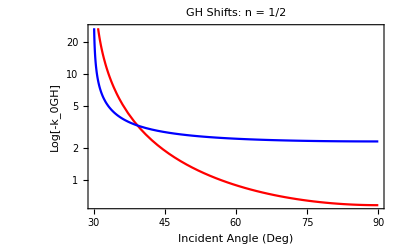

```mathematica
LogPlot[{-k0 GHshift$1[θ Degree,1/2],-k0 GHshift$2[θ Degree,1/2]},{θ,30 , 90 },PlotStyle->{Red,Blue},Frame->True,PlotLabel->font["GH Shifts: n = 1/2",14],FrameLabel->{font["Incident Angle (Deg)",12],font["Log[-k_0GH]",12]},GridLines->Automatic]
```

Here is the same plot but now in units for 600 nm incident light.

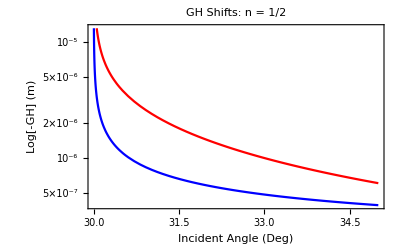

```mathematica
k0set = 2π/(600.*10^-9);

LogPlot[{-GHshift$1[θ Degree,1/2]/. k0->k0set,-GHshift$2[θ Degree,1/2]/. k0->k0set},{θ,30 , 35 },PlotStyle->{Red,Blue},Frame->True,PlotLabel->font["GH Shifts: n = 1/2",14],FrameLabel->{font["Incident Angle (Deg)",12],font["Log[-GH] (m)",12]},GridLines->Automatic]
```

#### Comparison with Artmann Formula for GH Shift

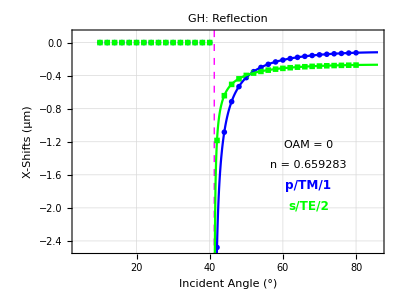

```mathematica
p$GH$analytic=Plot[{GHshift$1[θ Degree,1/1.5168]*10^6 /. k0->2π/(632.8*10^-9),GHshift$2[θ Degree,1/1.5168]*10^6 /. k0->2π/(632.8*10^-9)},{θ ,4,86},PlotStyle->{{Blue},{Green}},PlotRange->All];

p$GH=Show[p$Rxspinfinal,p$GH$analytic,PlotRange->{{4,86},{-2.5,0.1}},AspectRatio->0.75]
```

#### Prajapati’s Experimental SHEL Data

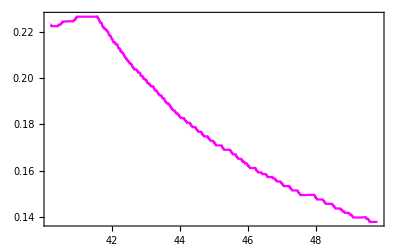

```mathematica
SetDirectory[NotebookDirectory[]];

exptdata$SHEL$plus = Drop[Import["Prajapati_Spin_Plus_SHEL_Expt_Data.txt","Table"],0];
exptdata$SHEL$minus = Drop[Import["Prajapati_Spin_Minus_SHEL_Expt_Data.txt","Table"],0];

p$prajapati$plus=ListLinePlot[{exptdata$SHEL$plus},Joined->True,Frame->True,PlotStyle->{Magenta, Thickness[.03]},PlotRange->All]
```

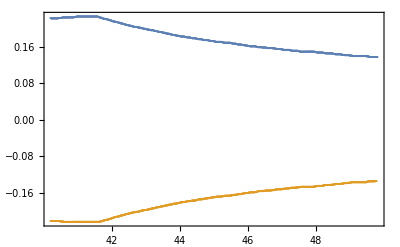

```mathematica
p$prajapati=ListLinePlot[{exptdata$SHEL$plus,exptdata$SHEL$minus},Joined->False,Frame->True,PlotMarkers->{●,2},PlotRange->All]
```

#### Bliokh’s Analytical Formula for SHEL Shifts

From [Bliokh_PRE_2007.pdf] Eq 58 we have Bliokh’s expression for the shifts

-Graphics-

polarizations: s/TE/2/perpendicular    and p/TM/1/parallel
m_c … ±ⅈ

ρ_c^I = 1

ρ_c^R = R_2/R_1

ρ_c^T = T_2/T_1

This is identical to Eq 5 in his 2006 PRL. As noted there, though, the equation is only appropriate for partial reflection. For total internal reflection we must use his PRL 2006 Eq 6:

-Graphics-

```mathematica
ArcSin[1/n Sin[θ]]; (* Snell *)
```

```mathematica
R2=(Cos[θ]-√(n^2-Sin[θ]^2))/(Cos[θ]+√(n^2-Sin[θ]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(n^2 Cos[θ]-√(n^2-Sin[θ]^2))/(n^2 Cos[θ]+√(n^2-Sin[θ]^2));(* Fresnel Reflection Coefficient: p/TM *)

T1=(2 n)/(n^2+Sec[θ] √(n^2-Sin[θ]^2));

T2=(2 Cos[θ])/(Cos[θ]+√(n^2-Sin[θ]^2));
```

```mathematica
(* mc = ⅈ for minus and -ⅈ for plus *)

Clear[mc];
kset = 2π/(632.8*10^-9);

ρcR =R2/R1;
θR = π-θ;
Clear[ΔR$subcrit,ΔR$supercrit];

ΔR$subcrit[θ_,n_,mc_] =Im[mc]/kset Cot[θ]((2ρcR Cos[θR]/Cos[θ]-1-ρcR^2)/(1+ρcR^2 Abs[mc]^2));

ΔR$supercrit[θ_,n_,mc_]  =(-2Cot[θ])/kset(Im[mc](1+Re[ρcR])+Re[mc]Im[ρcR])/(1+Abs[mc]^2);

Clear[ΔR];

ΔR[θ_,n_,mc_] := If[θ<ArcSin[n],ΔR$subcrit[θ,n,mc] ,ΔR$supercrit[θ,n,mc]];

ρcT =T2/T1;
θT = ArcSin[1/n Sin[θ]];
ΔT$subcrit =Im[mc]/kset Cot[θ]((2ρcT Cos[θT]/Cos[θ]-1-ρcT^2)/(1+ρcT^2 Abs[mc]^2));
```

```mathematica
10^6 ΔR [43 Degree,1/1.5168,-ⅈ]
```

0.200872

```mathematica
θbrewster = ArcTan[n]/Degree /.params$here;
p$brewster=Graphics[{Magenta,Dashing->Small,Line[{{θbrewster,-1},{θbrewster,1}}]}];

θcrit = ArcSin[n]/Degree /.params$here;
p$crit=Graphics[{Magenta,Dashing->Small,Line[{{θcrit,-1},{θcrit,1}}]}];
```

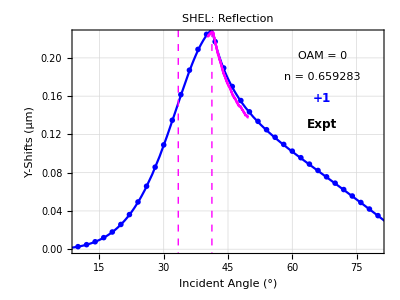

```mathematica
p$Rplus=ParametricPlot[{θ/Degree,10^6 ΔR [θ,1/1.5168,-ⅈ]},{θ,4 Degree,86 Degree},AspectRatio->.75,PlotStyle->Blue];

p$Rminus=ParametricPlot[{θ/Degree,10^6 ΔR [θ,1/1.5168,-ⅈ] },{θ,10 Degree,80 Degree},AspectRatio->.75,PlotStyle->Green];

p$Rbliokh=Show[{p$Rplus},PlotRange->All];

p$SHEL=Show[p$Ryspinfinal,p$Rbliokh,p$brewster,p$prajapati$plus,
Graphics[{Black,Text[font["Expt",12],{67,0.13}]},Background->White],p$crit,AspectRatio->0.75]
```

```mathematica
ArcCos[0.87]/Degree
```

29.5414

```mathematica
0.288*0.865
```

0.24912

#### Plot Graphic For Manuscript

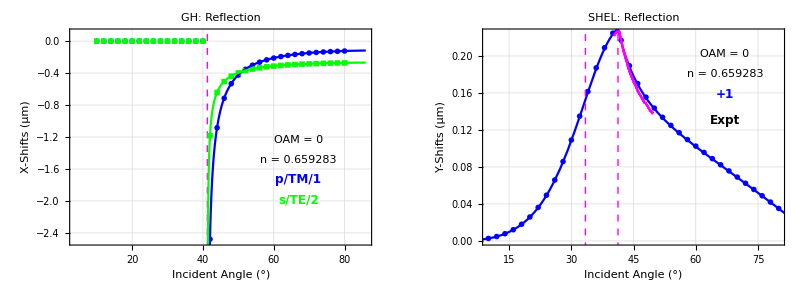

```mathematica
GraphicsRow[{p$GH,p$SHEL},ImageSize->800]
```

### Centroid Shifts versus Angle of Incidence: n = 1/1.5168, OAM = 5 (Glass/Air) FIG 5

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.5
```

33.6901

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

```mathematica
θcrit = ArcSin[n]/Degree /. n->1/1.5
```

41.8103

#### Analysis

```mathematica
Clear[plots,k0];

fontset = 6;

IFshift$tab$R1 = {};
IFshift$tab$R2 = {};
IFshift$tab$R3 = {};
IFshift$tab$R4 = {};
IFshift$tab$T1 = {};
IFshift$tab$T2 = {};
IFshift$tab$T3 = {};
IFshift$tab$T4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1/1.5168,θ->θloop Degree,k0->1,p->0,ℓ->5};

Print["Angle of Incidence: ",θloop,"°"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)

Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eR = {(f[[1]]R1-f[[2]]κy Cot[θ](R1+R2)),f[[2]]R2 + f[[1]]κy Cot[θ](R1+R2 ),-(f[[1]]R1 κx + f[[2]]R2  κy)} /. params$here;

eRtab = Table[eR /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

IFshift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

IFshift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, IFshift$R1={IFshift$Rx,IFshift$Ry},f$flag==2,IFshift$R2={IFshift$Rx,IFshift$Ry},f$flag==3,IFshift$R3={IFshift$Rx,IFshift$Ry},f$flag==4,IFshift$R4={IFshift$Rx,IFshift$Ry}];
Which[f$flag ==1, IFshift$T1={IFshift$Tx,IFshift$Ty},f$flag==2,IFshift$T2={IFshift$Tx,IFshift$Ty},f$flag==3,IFshift$T3={IFshift$Tx,IFshift$Ty},f$flag==4,IFshift$T4={IFshift$Tx,IFshift$Ty}];

},{f$flag,1,4}];

AppendTo[IFshift$tab$R1 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R1}];
AppendTo[IFshift$tab$R2 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R2}];
AppendTo[IFshift$tab$R3 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R3}];
AppendTo[IFshift$tab$R4 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R4}];

Print["TE x (Reflected) = ",IFshift$R1," μm"]; 
Print["  "];

},{θloop,10.0,80.0,2.0}]
```

Angle of Incidence: 10.°

TE x (Reflected) = {0,0.306897} μm

Angle of Incidence: 12.°

TE x (Reflected) = {0,0.392341} μm

Angle of Incidence: 14.°

TE x (Reflected) = {0,0.494859} μm

Angle of Incidence: 16.°

TE x (Reflected) = {0,0.621763} μm

Angle of Incidence: 18.°

TE x (Reflected) = {0,0.784259} μm

Angle of Incidence: 20.°

TE x (Reflected) = {0,1.0005} μm

Angle of Incidence: 22.°

TE x (Reflected) = {0,1.30194} μm

Angle of Incidence: 24.°

TE x (Reflected) = {0,1.74784} μm

Angle of Incidence: 26.°

TE x (Reflected) = {0,2.46386} μm

Angle of Incidence: 28.°

TE x (Reflected) = {0,3.76709} μm

Angle of Incidence: 30.°

TE x (Reflected) = {0,6.7364} μm

Angle of Incidence: 32.°

TE x (Reflected) = {0,18.7016} μm

Angle of Incidence: 34.°

TE x (Reflected) = {0,-50.4615} μm

Angle of Incidence: 36.°

TE x (Reflected) = {0,-14.1951} μm

Angle of Incidence: 38.°

TE x (Reflected) = {0,-10.5238} μm

Angle of Incidence: 40.°

TE x (Reflected) = {0,-12.2041} μm

Angle of Incidence: 42.°

TE x (Reflected) = {-2.47853,2.21152×10^-8} μm

Angle of Incidence: 44.°

TE x (Reflected) = {-1.08401,1.05281×10^-8} μm

Angle of Incidence: 46.°

TE x (Reflected) = {-0.714855,4.91768×10^-9} μm

Angle of Incidence: 48.°

TE x (Reflected) = {-0.533106,2.03806×10^-9} μm

Angle of Incidence: 50.°

TE x (Reflected) = {-0.424296,4.9234×10^-10} μm

Angle of Incidence: 52.°

TE x (Reflected) = {-0.35211,-2.97694×10^-10} μm

Angle of Incidence: 54.°

TE x (Reflected) = {-0.301018,-7.32785×10^-10} μm

Angle of Incidence: 56.°

TE x (Reflected) = {-0.263198,-9.04532×10^-10} μm

Angle of Incidence: 58.°

TE x (Reflected) = {-0.234268,-9.10257×10^-10} μm

Angle of Incidence: 60.°

TE x (Reflected) = {-0.211581,-8.35833×10^-10} μm

Angle of Incidence: 62.°

TE x (Reflected) = {-0.193446,-7.67135×10^-10} μm

Angle of Incidence: 64.°

TE x (Reflected) = {-0.178734,-6.81261×10^-10} μm

Angle of Incidence: 66.°

TE x (Reflected) = {-0.166665,-5.55314×10^-10} μm

Angle of Incidence: 68.°

TE x (Reflected) = {-0.156682,-4.57991×10^-10} μm

Angle of Incidence: 70.°

TE x (Reflected) = {-0.148381,-3.89292×10^-10} μm

Angle of Incidence: 72.°

TE x (Reflected) = {-0.141462,-3.26318×10^-10} μm

Angle of Incidence: 74.°

TE x (Reflected) = {-0.135697,-2.23271×10^-10} μm

Angle of Incidence: 76.°

TE x (Reflected) = {-0.130916,-1.54572×10^-10} μm

Angle of Incidence: 78.°

TE x (Reflected) = {-0.126984,-1.14498×10^-10} μm

Angle of Incidence: 80.°

TE x (Reflected) = {-0.123802,0} μm

#### Data Record

```mathematica
params$here = {wk->20000.,n->1/1.5168,θ->θloop Degree,k0->1,p->0,ℓ->5};
```

```mathematica
IFshift$tab$R4
```

IFshift$tab$R4

```mathematica
shift$tab$R1={{5,10.,{0,0.3068974965265861}},{5,12.000000000000002,{0,0.3923406813659754}},{5,14.,{0,0.4948593306986899}},{5,16.,{0,0.6217629726885143}},{5,18.,{0,0.7842588653122083}},{5,20.,{0,1.0005048547329012}},{5,22.,{0,1.301940068493657}},{5,24.000000000000004,{0,1.7478436633495706}},{5,26.,{0,2.4638565103613543}},{5,28.,{0,3.7670905103407555}},{5,29.999999999999996,{0,6.736401423126062}},{5,32.,{0,18.701551675024437}},{5,34.,{0,-50.46146217064158}},{5,36.,{0,-14.19511498658346}},{5,38.,{0,-10.523794540603744}},{5,40.,{0,-12.204143386169315}},{5,42.,{-2.478529919992644,2.2115232069368972*^-8}},{5,44.,{-1.0840149441716165,1.0528064140711762*^-8}},{5,46.,{-0.7148546464089293,4.917676507271019*^-9}},{5,48.00000000000001,{-0.5331056516355029,2.0380591811274537*^-9}},{5,50.,{-0.4242963443258601,4.923401392611265*^-10}},{5,52.,{-0.35211002631428784,-2.976940376927741*^-10}},{5,54.,{-0.30101832174227156,-7.32785323551444*^-10}},{5,56.,{-0.2631984167431948,-9.045318837588137*^-10}},{5,58.00000000000001,{-0.23426815530319314,-9.102567690990594*^-10}},{5,59.99999999999999,{-0.21158107128987477,-8.358332596758658*^-10}},{5,62.,{-0.1934461658758313,-7.67134635592918*^-10}},{5,64.,{-0.1787343800710515,-6.812613554892331*^-10}},{5,66.,{-0.16666487716769665,-5.553138780038287*^-10}},{5,68.,{-0.15668200450049832,-4.5799082721965247*^-10}},{5,70.,{-0.1483810292494442,-3.8929220313670464*^-10}},{5,72.,{-0.14146152676110615,-3.263184643940024*^-10}},{5,74.,{-0.13569715432764506,-2.2327052826958058*^-10}},{5,76.,{-0.13091550628852927,-1.5457190418663273*^-10}},{5,78.,{-0.12698438174806878,-1.1449770680491312*^-10}},{5,80.,{-0.12380225308213984,0}}};
```

```mathematica
shift$tab$R2={{5,10.,{0,-0.27635267094371885}},{5,12.000000000000002,{0,-0.33636170249065844}},{5,14.,{0,-0.3992641708304861}},{5,16.,{0,-0.46584191417675697}},{5,18.,{0,-0.5370705611116335}},{5,20.,{0,-0.6142034325761455}},{5,22.,{0,-0.6989008650778407}},{5,24.000000000000004,{0,-0.7934382810301881}},{5,26.,{0,-0.9010579748445738}},{5,28.,{0,-1.0266004160566937}},{5,29.999999999999996,{0,-1.1777245292177894}},{5,32.,{0,-1.367504733279125}},{5,34.,{0,-1.620731475030476}},{5,36.,{0,-1.9924212477277654}},{5,38.,{0,-2.642411990015403}},{5,40.,{0,-4.439442935515769}},{5,42.,{-1.1843193785421804,2.2132406725389708*^-8}},{5,44.,{-0.6425437274529777,1.0550963682072744*^-8}},{5,46.,{-0.5060718700481979,4.923401392611265*^-9}},{5,48.00000000000001,{-0.4386651331116142,2.0266094104469624*^-9}},{5,50.,{-0.39753154990547285,4.6371571255989817*^-10}},{5,52.,{-0.36957276143351353,-3.377682350744937*^-10}},{5,54.,{-0.3492788953606694,-7.270604382111984*^-10}},{5,56.,{-0.33388551257327237,-8.873572277380768*^-10}},{5,58.00000000000001,{-0.32183826934656895,-9.102567690990594*^-10}},{5,59.99999999999999,{-0.3121903120208837,-8.701825717173397*^-10}},{5,62.,{-0.3043295148052343,-7.67134635592918*^-10}},{5,64.,{-0.29784162188206287,-6.698115848087418*^-10}},{5,66.,{-0.2924359880531753,-5.610387633440743*^-10}},{5,68.,{-0.28790272484145724,-4.5799082721965247*^-10}},{5,70.,{-0.2840867091335868,-3.66392661775722*^-10}},{5,72.,{-0.2808711611689648,-2.976940376927741*^-10}},{5,74.,{-0.2781669113815565,-2.1182075758908928*^-10}},{5,76.,{-0.2759051848231078,-1.5457190418663273*^-10}},{5,78.,{-0.27403263719521426,0}},{5,80.,{-0.2725078779833331,0}}};
```

```mathematica
shift$tab$R3={{5,10.,{0,-0.010087154688231112}},{5,12.000000000000002,{0,-0.018499596096031957}},{5,14.,{0,-0.03151954750348848}},{5,16.,{0,-0.05103084701424006}},{5,18.,{0,-0.07965199032197914}},{5,20.,{0,-0.12102382434096033}},{5,22.,{0,-0.18018740294881494}},{5,24.000000000000004,{0,-0.26406313611980564}},{5,26.,{0,-0.38203885188161674}},{5,28.,{0,-0.5467058175043968}},{5,29.999999999999996,{0,-0.774973406506867}},{5,32.,{0,-1.0905461003280985}},{5,34.,{0,-1.5313891271816908}},{5,36.,{0,-2.1760351177865993}},{5,38.,{0,-3.2589703139188644}},{5,40.,{0,-6.1324235465338806}},{5,42.,{-1.8314246720724927,0.2170046204947977}},{5,44.,{-0.8632793425590745,0.18946078802249774}},{5,46.,{-0.6104632611568424,0.17010541585696062}},{5,48.00000000000001,{-0.48588539362444594,0.1554356272786225}},{5,50.,{-0.41091394749064647,0.14363697700752331}},{5,52.,{-0.36084139364776774,0.13367680147836478}},{5,54.,{-0.32514860790169603,0.12492559295749528}},{5,56.,{-0.2985419637021777,0.11697935353415852}},{5,58.00000000000001,{-0.2780532111054805,0.10956856393051902}},{5,59.99999999999999,{-0.26188569020125835,0.10250818282254101}},{5,62.,{-0.24888783869462827,0.09566859065960949}},{5,64.,{-0.23828799916463095,0.08895789337413194}},{5,66.,{-0.2295504306468003,0.0823107044458146}},{5,68.,{-0.2222923625785322,0.07568078146826453}},{5,70.,{-0.2162338669359107,0.06903603910977153}},{5,72.,{-0.21116634158920805,0.062355074697569915}},{5,74.,{-0.20693203036713814,0.05562468086393086}},{5,76.,{-0.203410342985345,0.04883801864937715}},{5,78.,{-0.20050850682960694,0.04199324049601223}},{5,80.,{-0.19815506282200324,0.03509242439981737}}};
```

```mathematica
shift$tab$R4={{5,10.,{0,-0.015396608766011139}},{5,12.000000000000002,{0,-0.027956189694608405}},{5,14.,{0,-0.04707631516943819}},{5,16.,{0,-0.07520119234894708}},{5,18.,{0,-0.11562078091964131}},{5,20.,{0,-0.17276227650909298}},{5,22.,{0,-0.25254738209399896}},{5,24.000000000000004,{0,-0.3628041196809905}},{5,26.,{0,-0.5137090543473602}},{5,28.,{0,-0.7182651338812183}},{5,29.999999999999996,{0,-0.9930347558667256}},{5,32.,{0,-1.3601730245451547}},{5,34.,{0,-1.8545767880582835}},{5,36.,{0,-2.5503060228508057}},{5,38.,{0,-3.676753506474795}},{5,40.,{0,-6.581752643301319}},{5,42.,{-1.8314246264394318,-0.21700457624143404}},{5,44.,{-0.8632793290655197,-0.18946076696064457}},{5,46.,{-0.6104632553002848,-0.17010540601015786}},{5,48.00000000000001,{-0.4858853910940467,-0.15543562323112856}},{5,50.,{-0.41091394677503584,-0.14363697603429282}},{5,52.,{-0.36084139411720834,-0.13367680213672659}},{5,54.,{-0.32514860917262056,-0.12492559436009218}},{5,56.,{-0.29854196560856455,-0.11697935527452365}},{5,58.00000000000001,{-0.2780532135385567,-0.10956856574530767}},{5,59.99999999999999,{-0.2618856930980504,-0.10250818455718126}},{5,62.,{-0.24888784196353783,-0.09566859219387876}},{5,64.,{-0.23828800277703363,-0.08895789470230535}},{5,66.,{-0.22955043457407165,-0.0823107055793419}},{5,68.,{-0.22229236680922246,-0.07568078234989686}},{5,70.,{-0.21623387143567058,-0.06903603985400662}},{5,72.,{-0.21116634631223846,-0.06235507524715891}},{5,74.,{-0.20693203533061372,-0.05562468127039771}},{5,76.,{-0.20341034812629202,-0.04883801897569561}},{5,78.,{-0.20050851213657567,-0.04199324070783299}},{5,80.,{-0.1981550682720941,-0.03509242457728882}}};
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];


RΔx$plotdata = Table[{R1x$plotdata[[i,1]],R1x$plotdata[[i,2]]-R2x$plotdata[[i,2]]},{i,1,Length[R1x$plotdata]}];

RΔy$plotdata = Table[{R1y$plotdata[[i,1]],R1y$plotdata[[i,2]]-R2y$plotdata[[i,2]]},{i,1,Length[R1y$plotdata]}];
```

#### Reflection Plots

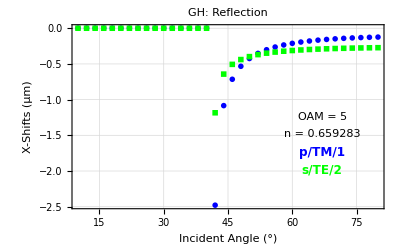

```mathematica
params$here = {wk->20000.,n->1/1.5168,θ->θloop Degree,k0->1,p->0,ℓ->5};

dat=Join[R1x$plotdata,R2x$plotdata];

p$Rxspin=ListLinePlot[{R1x$plotdata,R2x$plotdata},PlotMarkers->{{Graphics[Disk[]],.03},{Graphics[Rectangle[]],.02},{Graphics[Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]],.03}},Joined->False,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{{Thickness[.006],Blue},{Thickness[.006],Green},Darker[Red]},FrameLabel->{font["Incident Angle (°)",14],font["X-Shifts (μm)",14]},PlotLabel->font["GH: Reflection",16]];

vmax= Max[Transpose[dat][[2]]];
vmin= Min[Transpose[dat][[2]]];


p$Rxspinfinal = Show[p$Rxspin,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{67,vmin + 0.5 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{67,vmin + 0.4(vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font["p/TM/1",12],{67,vmin + 0.3(vmax-vmin)}]},Background->White],
Graphics[{Green,Text[font["s/TE/2",12],{67,vmin + 0.2(vmax-vmin)}]},Background->White]
]
```

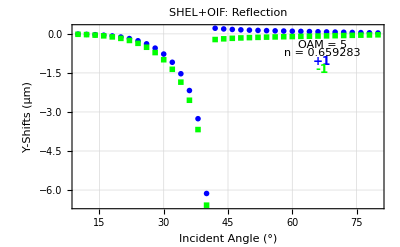

```mathematica
dat=Join[R3y$plotdata,R3y$plotdata];

p$Ryspin=ListLinePlot[{R3y$plotdata,R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.03},{Graphics[Rectangle[]],.02},{Graphics[Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]],.03}},Joined->False,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{{Thickness[.006],Blue},{Thickness[.006],Green},Darker[Red]},FrameLabel->{font["Incident Angle (°)",14],font["Y-Shifts (μm)",14]},PlotLabel->font["SHEL+OIF: Reflection",16]];

vmax= Max[Transpose[dat][[2]]];
vmin= Min[Transpose[dat][[2]]];


p$Ryspinfinal = Show[p$Ryspin,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{67,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{67,vmin + 0.85(vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font["+1",12],{67,vmin + 0.8(vmax-vmin)}]},Background->White],
Graphics[{Green,Text[font["-1",12],{67,vmin + 0.75(vmax-vmin)}]},Background->White]
]
```

TM - TE, Y-Shift

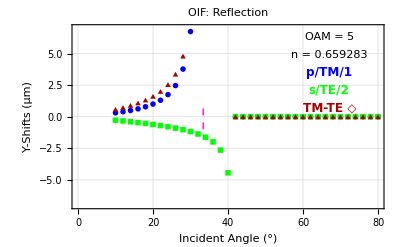

```mathematica
dat=Join[R1y$plotdata,R2y$plotdata];
vmax= 7;
vmin= -7;

p$RyTETM=ListLinePlot[{R1y$plotdata,R2y$plotdata,RΔy$plotdata},PlotMarkers->{{Graphics[Disk[]],.03},{Graphics[Rectangle[]],.02},{Graphics[Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]],.03}},Joined->False,GridLines->Automatic,Frame->True,PlotRange->{vmin,vmax},PlotStyle->{{Thickness[.006],Blue},{Thickness[.006],Green},Darker[Red]},FrameLabel->{font["Incident Angle (°)",14],font["Y-Shifts (μm)",14]},PlotLabel->font["OIF: Reflection",16]];

p$RyTETMfinal = Show[p$RyTETM,p$brewster,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{67,vmin + 0.95 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{67,vmin + 0.85(vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font["p/TM/1",12],{67,vmin + 0.75(vmax-vmin)}]},Background->White],
Graphics[{Green,Text[font["s/TE/2",12],{67,vmin + 0.65(vmax-vmin)}]},Background->White],
Graphics[{Darker[Red],Text[font["TM-TE ◇",12],{67,vmin + 0.55 (vmax-vmin)}]},Background->White]
]
```

#### Construction of Artmann Formula for the Goos-Hanchen Shifts

The work below does not derive Artmann’s formula for the GH shift. Rather, Artmann’s formula is used to get an explicit expression for the GH shift. However, in the application section in which a Gaussian beam is considered analytically, I derive Artmann’s formula explicitly by analytically calculating the centroid of the reflected beam. (That was fun and cool to do!)

Start by defining the two reflection coefficients. These will be complex valued for angles of incidence greater than the critical angle. The existence of a critical angle implies that n_2 < n_1--i.e. that the wave impinges on a material with a lower dielectric constant.

```mathematica
Clear[R1$Art,R2$Art,β$Art,n];

R2$Art=(Cos[β$Art]-√(n^2-Sin[β$Art]^2))/(Cos[β$Art]+√(n^2-Sin[β$Art]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1$Art=(-n^2 Cos[β$Art]+√(n^2-Sin[β$Art]^2))/(n^2 Cos[β$Art]+√(n^2-Sin[β$Art]^2));(* Fresnel Reflection Coefficient: p/TM *)
```

The GH shift can be estimated from the phase of these reflection coefficients. These phases, in turn, can be obtained in an analytically simple form or just by brute force. The approaches are shown to be equivalent below.

The brute force approach is:

```mathematica
Clear[Φ1,Φ2];

Φ1[β$Art_,n_]=FullSimplify[ArcTan[Re[R1],Im[R1]]];

Φ2[β$Art_,n_]=FullSimplify[ArcTan[Re[R2 ],Im[R2]]];
```

The derivative of these expressions with respect to β gives the GH shift:

GH_λ := (∂_β Φ_λ)/k_0

This is written in the coordinate system of the reflected beam, and the shift will come out to be negative. This is still “up and to the right” in our fixed frame though. If we use the expressions for Φ directly, the resulting formulae are ugly and do not offer any insights. We can analytically derive equivalent phase representations, with only a little effort, that work much better. First separate the reflection coefficients into real and imaginary parts.

```mathematica
((-n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2))/(n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2)))((n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2))/(n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2)))
```

(-n^2 (√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])+ⅈ √(1-n^2-(√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])^2))/(n^2 (√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])+ⅈ √(1-n^2-(√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])^2))

```mathematica
((-n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2))(n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2))
```

1/(-n^2+n^4 Cos[θ]^2+Sin[θ]^2)(n^2 (√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])-ⅈ √(1-n^2-(√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])^2)) (-n^2 (√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])+ⅈ √(1-n^2-(√(1-κx^2-κy^2) Cos[θ]-κx Sin[θ])^2))

```mathematica
R1$analytic=(-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2)+ⅈ 2 n^2 Cos[β] √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2);
```

```mathematica
R2$analytic=((Cos[θ])^2-2ⅈ Cos[θ] √(1-n^2-Cos[θ]^2)-(1-n^2-Cos[θ]^2))/((Cos[θ])^2+1-n^2-Cos[θ]^2);
```

Then the phases are

```mathematica
Clear[Φ1$analytic];
Φ1$analytic[θ_,n_]=FullSimplify[ArcTan[-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2),2 n^2 Cos[θ] √(Sin[θ]^2-n^2)] ,{θ>0,n>0,(Sin[θ]^2-n^2)>0}]
```

ArcTan[-n^2-n^4 Cos[θ]^2+Sin[θ]^2,2 n^2 Cos[θ] √(-n^2+Sin[θ]^2)]

```mathematica
Clear[Φ2$analytic];
Φ2$analytic[θ_,n_]=FullSimplify[ArcTan[(Cos[θ])^2-(1-n^2-Cos[θ]^2),-2Cos[θ] √(1-n^2-Cos[θ]^2)] ,{θ>0,n>0,1-n^2-Cos[θ]^2>0}]
```

ArcTan[n^2+Cos[2 θ],-2 Cos[θ] √(1-n^2-Cos[θ]^2)]

Below is a comparison of the two expressions for Φ_1. They are clearly equivalent.

```mathematica
Plot[{Φ1[θ,1/2],Φ1$analytic[θ,1/2]},{θ,30 Degree, 50 Degree},PlotStyle->{{Thickness[.01],Red},Blue},Frame->True,FrameLabel->{font["θ (Deg)",10],font["R_1 Phase (rad)",10]},PlotLabel->font["Phase 1 Comparison",14]]
```

-Graphics-

Below is a comparison of the two expressions for Φ_2. They are clearly equivalent.

```mathematica
Plot[{Φ2[θ,1/2],Φ2$analytic[θ,1/2]},{θ,30 Degree, 50 Degree},PlotStyle->{{Thickness[.01],Red},Blue},Frame->True,FrameLabel->{font["θ (Deg)",10],font["R_2 Phase (rad)",10]},PlotLabel->font["Phase 2 Comparison",14]]
```

-Graphics-

These formula can be used to calculate the GH shifts for each polarization using Artmann’s formulae:

```mathematica
Clear[GHshift$1,GHshift$2,k0];
GHshift$1[θ_,n_]=1/k0 FullSimplify[D[Φ1$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]

GHshift$2[θ_,n_]=1/k0 FullSimplify[D[Φ2$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]
```

(4 n^2 Sin[θ])/(k0 (-1+n^2+(1+n^2) Cos[2 θ]) √(-n^2+Sin[θ]^2))

-(2 √2 Sin[θ])/(k0 √(1-2 n^2-Cos[2 θ]))

These are very small shifts in general. For instance, for 600 nm light and n = 0.5, the critical angle is 30°. At 35°, the GH shift for polarization 1 is only 600 nm. This is shown below.

```mathematica
Print["GH_1 for 600 nm light: ",GHshift$1[35. Degree,1/2]/. k0->2π/(600.0*10^-9)," meters"]
```

GH_1 for 600 nm light: -6.0434×10^-7 meters

Here is a plot of the GH shifts for both polarizations.

```mathematica
LogPlot[{-k0 GHshift$1[θ Degree,1/2],-k0 GHshift$2[θ Degree,1/2]},{θ,30 , 90 },PlotStyle->{Red,Blue},Frame->True,PlotLabel->font["GH Shifts: n = 1/2",14],FrameLabel->{font["Incident Angle (Deg)",12],font["Log[-k_0GH]",12]},GridLines->Automatic]
```

-Graphics-

Here is the same plot but now in units for 600 nm incident light.

```mathematica
k0set = 2π/(600.*10^-9);

LogPlot[{-GHshift$1[θ Degree,1/2]/. k0->k0set,-GHshift$2[θ Degree,1/2]/. k0->k0set},{θ,30 , 35 },PlotStyle->{Red,Blue},Frame->True,PlotLabel->font["GH Shifts: n = 1/2",14],FrameLabel->{font["Incident Angle (Deg)",12],font["Log[-GH] (m)",12]},GridLines->Automatic]
```

-Graphics-

#### Comparison with Artmann Formula for GH Shift

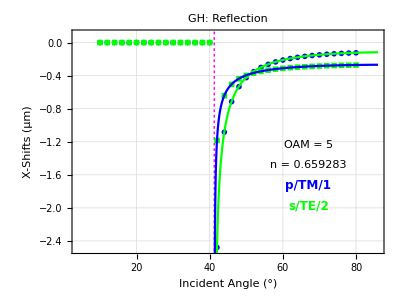

```mathematica
p$GH$analytic=Plot[{GHshift$1[θ Degree,1/1.5168]*10^6 /. k0->2π/(632.8*10^-9),GHshift$2[θ Degree,1/1.5168]*10^6 /. k0->2π/(632.8*10^-9)},{θ ,4,86},PlotStyle->{{Green},{Blue}},PlotRange->All];

p$GH=Show[p$Rxspinfinal,p$GH$analytic,p$crit,PlotRange->{{4,86},{-2.5,0.1}},AspectRatio->0.75]
```

#### Dasgupta’s Experimental OIF Data for OAM = 5

Here is experimental data, obtained using Data Thirf, associated with the OIF shift of LG beams as a function of angle of incidence. The data was taken from the experimental measurements shown below. This is Figure 4 of Dasgupta, P.K. Gupta / Optics Communications 257 (2006) 91–96 [IF_Measurement_Dasgupta_OptComm_2006.pdf]. 

This is used in the following analysis:  n = 1.5, OAM = 5, 4 mm Beam. I will eventually re-run this analysis with n = 1.5168 (BK7).

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];

exptdata = Drop[Import["IF_Expt_Data_Dasgupta_for_Mathematica.txt","Table"],1];

temp = Table[{exptdata[[i,1]],exptdata[[i,2]]/1000.},{i,1,Length[exptdata]}];

exptdata = temp
```

{{27.069,0.784726},{30.0862,0.995099},{33.1034,1.10047},{36.1207,1.18484},{38.9655,1.5737},{41.8103,1.9888},{71.9828,-1.89248},{75,-1.6716},{78.0172,-1.48223},{81.0345,-1.20886}}

```mathematica
p$dasgupta=ListLinePlot[exptdata,Joined->False,Frame->True,PlotStyle->{Black},PlotMarkers->{{Graphics[Disk[]],.05}},PlotRange->All]
```

-Graphics-

```mathematica
k0set= (2 π)/(632.8*10^-9);

thicknesstab = Table[{L, ToString[0.1Round[10L/k0set*10^6]]},{L,10,100,10}];

thicknesstab = PrependTo[thicknesstab,{"Lk_0  ","Air Gap (μm)"}];

TableForm[thicknesstab]
```

Lk_0   | Air Gap (μm)
10 | 1.
20 | 2.
30 | 3.
40 | 4.
50 | 5.
60 | 6.
70 | 7.
80 | 8.1
90 | 9.1
100 | 10.1

For purely Gaussian beams, there is no OAM but there is still an IF shift. This was measured by in OPTICS LETTERS / Vol. 39, No. 15 / August 1, 2014 [IF_GH_Measurement_ Prajapati_Opt_Lett_2014.pdf] with the key result shown in panel (b) below. This is for a glass-to-air interface with n = 1/1.5168 and He-Ne laser (632.8 nm). The critical angle is 41.8°.

-Graphics-

#### Bliokh’s Analytical Formula for SHEL Shifts

From [Bliokh_PRE_2007.pdf] Eq 58 we have Bliokh’s expression for the shifts

-Graphics-

polarizations: s/TE/2/perpendicular and p/TM/1/parallel
m_c … ±ⅈ

ρ_c^I = 1

ρ_c^R = R_2/R_1

ρ_c^T = T_2/T_1

This is identical to Eq 5 in his 2006 PRL. As noted there, though, the equation is only appropriate for partial reflection. For total internal reflection we must use his PRL 2006 Eq 6:

-Graphics-

```mathematica
ArcSin[1/n Sin[θ]]; (* Snell *)
```

```mathematica
R2=(Cos[θ]-√(n^2-Sin[θ]^2))/(Cos[θ]+√(n^2-Sin[θ]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(n^2 Cos[θ]-√(n^2-Sin[θ]^2))/(n^2 Cos[θ]+√(n^2-Sin[θ]^2));(* Fresnel Reflection Coefficient: p/TM *)

T1=(2 n)/(n^2+Sec[θ] √(n^2-Sin[θ]^2));

T2=(2 Cos[θ])/(Cos[θ]+√(n^2-Sin[θ]^2));
```

```mathematica
(* mc = ⅈ for minus and -ⅈ for plus *)

Clear[mc];
kset = 2π/(632.8*10^-9);

ρcR =R2/R1;
θR = π-θ;
Clear[ΔR$subcrit,ΔR$supercrit];

ΔR$subcrit[θ_,n_,mc_] =Im[mc]/kset Cot[θ]((2ρcR Cos[θR]/Cos[θ]-1-ρcR^2)/(1+ρcR^2 Abs[mc]^2));

ΔR$supercrit[θ_,n_,mc_]  =(-2Cot[θ])/kset(Im[mc](1+Re[ρcR])+Re[mc]Im[ρcR])/(1+Abs[mc]^2);

Clear[ΔR];

ΔR[θ_,n_,mc_] := If[θ<ArcSin[n],ΔR$subcrit[θ,n,mc] ,ΔR$supercrit[θ,n,mc]];

ρcT =T2/T1;
θT = ArcSin[1/n Sin[θ]];
ΔT$subcrit =Im[mc]/kset Cot[θ]((2ρcT Cos[θT]/Cos[θ]-1-ρcT^2)/(1+ρcT^2 Abs[mc]^2));
```

```mathematica
10^6 ΔR [43 Degree,1/1.5168,-ⅈ]
```

0.200872

```mathematica
θbrewster = ArcTan[n]/Degree /.params$here;
p$brewster=Graphics[{Magenta,Dashing->Tiny,Line[{{θbrewster,-100},{θbrewster,100}}]}];

θcrit = ArcSin[n]/Degree /.params$here;
p$crit=Graphics[{Magenta,Dashing->Tiny,Line[{{θcrit,-100},{θcrit,100}}]}];
```

```mathematica
p$Rplus=ParametricPlot[{θ/Degree,10^6 ΔR [θ,1/1.5168,-ⅈ]},{θ,4 Degree,86 Degree},AspectRatio->.75,PlotStyle->Blue];

p$Rminus=ParametricPlot[{θ/Degree,10^6 ΔR [θ,1/1.5168,ⅈ] },{θ,10 Degree,80 Degree},AspectRatio->.75,PlotStyle->Green];

p$Rbliokh=Show[{p$Rplus,p$Rminus},PlotRange->All];
```

```mathematica
ArcCos[0.87]/Degree
```

29.5414

```mathematica
0.288*0.865
```

0.24912

#### Plot Graphic For Manuscript

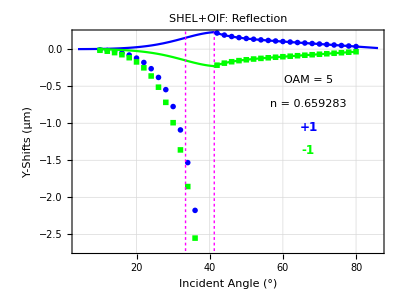

```mathematica
p$SHEL=Show[p$Ryspinfinal,p$Rbliokh,p$brewster,p$crit,AspectRatio->0.75,PlotRange->{-2.7,.2}]
```

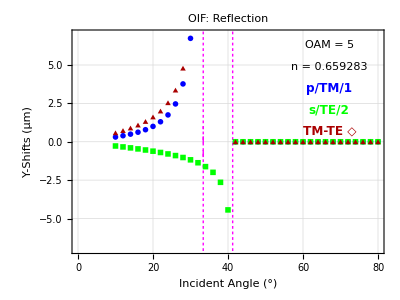

```mathematica
p$OIFplusSHEL=Show[{p$RyTETMfinal,p$brewster,p$crit},AspectRatio->0.75]
```

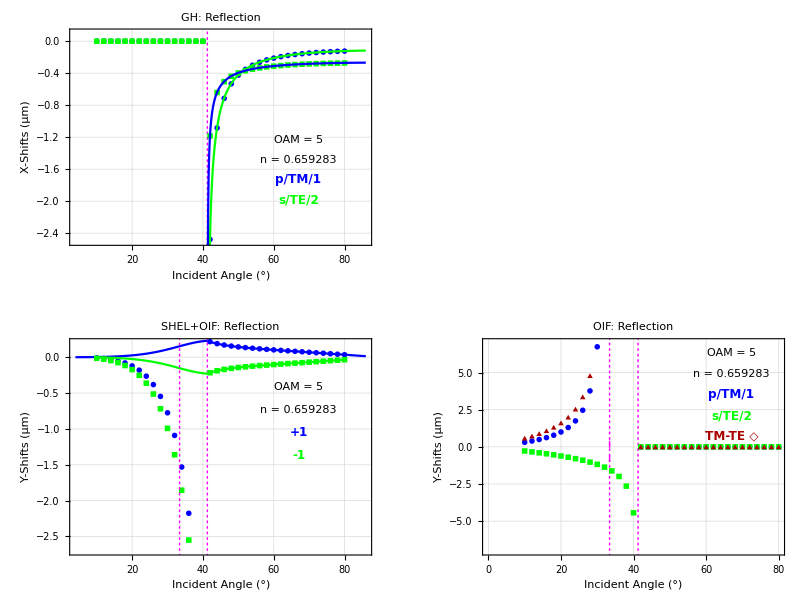

```mathematica
GraphicsGrid[{{p$GH},{p$SHEL,p$OIFplusSHEL}},ImageSize->800]
```